## Initialization

### Package dependencies

```mathematica
Needs["EPToolbox`",NotebookDirectory[]<>"Packages/EPToolbox.m"]
```

```mathematica
Needs["ARMSupport`",NotebookDirectory[]<>"Packages/ARMSupport.m"]
Print[$ARMSupportVersion]
```

ARMSupport v1.0.15, Wed 8 Jun 2016 12:46:18

```mathematica
Needs["MaTeX`",NotebookDirectory[]<>"Packages/MaTeX.m"]
SetOptions[MaTeX,"Preamble"->{"\\usepackage{color,txfonts} \\usepackage{lmodern}"}];
```

```mathematica
$OutputDirectory=NotebookDirectory[]<>"../5-Quantum-orbits/Figures/";
```

### Parameters

```mathematica
onemicronpars={0.05,45.6/1000,1.07};
mainpars={0.05,0.057,1.07};
PullenPars={0.05,45.6/3100,1.07};
```

### Minor utilities

```mathematica
Integerize[x_]:=If[Round[x]==x,Rationalize[x],x]
SetAttributes[Integerize,Listable]
```

```mathematica
(*{# π,MaTeX[StringReplace[ToString[Numerator[#]]<>"\\pi/"<>ToString[Denominator[#]],{"/1"->"","1\\pi"->"\\pi","0\\pi"->"0"}],FontSize->9]}&/@Range[0,2,1/2]*)
```

### Automatically save a copy with no output

To turn it on:

```mathematica
SetOptions[
EvaluationNotebook[],
NotebookEventActions->{
{"MenuCommand","Save"}:>(
NotebookSave[];
Block[{nb,tempfile,cleanfile},
tempfile=FileNameJoin[{NotebookDirectory[],"temp.nb"}];
cleanfile=FileNameJoin[{DirectoryName[#],"Clean",StringReplace[FileNameTake[#],{".nb"->" - clean.nb"}]}]&[NotebookFileName[]];
CopyFile[NotebookFileName[],tempfile];
nb=NotebookOpen[tempfile,Visible->False];
NotebookFind[nb,"Output",All,CellStyle];
NotebookDelete[nb];
NotebookSave[nb,cleanfile];
NotebookClose[nb];
Run["sed -i 's/Visible->True/Visible->True/g' ",StringReplace[cleanfile,{" "->"\\ ","\\"->"\\\\"}]];
DeleteFile[tempfile];
]
)
}
];
```

To turn it off:

```mathematica
SetOptions[EvaluationNotebook[],NotebookEventActions->{}]
```

## Time and space trajectories and contours

### Figure 5B - standard time contour

```mathematica
Block[{F, ω, κ,tss},
{F, ω, κ}=mainpars;
tss=ts[{0, 0, 0.5}, {F, ω, κ}];
figure5B=Show[{
Graphics[{Blue,PointSize[0.015],Point[{Re[ω tss],Im[ω tss]}]}],
Graphics[{Blue,Thickness[0.004],Arrowheads[0.03],Arrow[{{Re[ω tss],Im[ω tss]},{Re[ω tss],0}}],Arrow[{{Re[ω tss],0},{2.1π,0}}]}],
Graphics[Inset[MaTeX["t_s",FontSize->9],{Re[ω tss],Im[ω tss]},Scaled[{1.05,0.25}]]],
Graphics[Inset[MaTeX["t_0",FontSize->9],{Re[ω tss],0},Scaled[{0.85,0.9}]]]
}
,Frame->True,Axes->{True,True}
,PlotRange->{{-0.13,1.05}2π,{-0.75,1.7}}
,AspectRatio->Automatic
,ImageSize->180
,FrameTicks->{{{#,MaTeX[#,FontSize->9]}&/@Range[-1,2,1],{}},{
{# π,MaTeX[StringReplace[ToString[Numerator[#]]<>"\\pi/"<>ToString[Denominator[#]],{"/1"->"","1\\pi"->"\\pi","0\\pi"->"0"}],FontSize->9]}&/@Range[0,2,1/2]
,{}}}
,Method->{"AxesInFront"->False}
,AxesStyle->GrayLevel[0.8]
,FrameLabel->{MaTeX["\\mathrm{Re}(\\omega t)",FontSize->9],MaTeX["\\mathrm{Im}(\\omega t)",FontSize->9]}
]
]
FileByteCount[Export[$OutputDirectory<>"figure5B.pdf",Show[figure5B,ImageSize->220]]]
```

9041

### Figure 5C - z trajectories on the downward leg of the time contour

```mathematica
figure5Cparameters=onemicronpars; (* {F, ω, κ} *)
```

```mathematica
figure5C=Block[{F,ω,κ,λ=45.6/(1000 ω),pplist,tslist,inset},
{F,ω,κ}=figure5Cparameters;
pplist=Range[-1,1,0.2]F/ω;
tslist=(ts[{0, 0, #}, {F, ω, κ}]&/@pplist);

inset=Show[Join[{
Graphics[{White,EdgeForm[],Rectangle[{-0.82,-0.05},{0.82,1.18}]}],
Graphics[{GrayLevel[0.8],Line[{{-0.82,0},{0.82,0}}],Line[{{0,-0.05},{0,1.18}}]}]
},
Table[{
Graphics[{Blue,PointSize[0.03],Point[{Re[ω ts[{0,0,pp}, {F,ω,κ}]],Im[ω ts[{0,0,pp}, {F,ω,κ}]]}]}],
Graphics[{Blue,Thickness[0.01],Arrowheads[0.05],Arrow[{{Re[ω ts[{0,0,pp}, {F,ω,κ}]],Im[ω ts[{0,0,pp}, {F,ω,κ}]]},{Re[ω ts[{0,0,pp}, {F,ω,κ}]],0}}]}],
Graphics[Text[
Style[If[IntegerQ[Round[ω pp/ F,1/10]],ToString[IntegerPart[ω pp/ F]],ToString[NumberForm[ω pp/ F,2]]],5.7]
,{Re[ω ts[{0,0,pp}, {F,ω,κ}]],Im[ω ts[{0,0,0}, {F,ω,κ}]]+1.1(Im[ω ts[{0,0,pp}, {F,ω,κ}]]-Im[ω ts[{0,0,0}, {F,ω,κ}]])},{0,-1.4}]]
},{pp,pplist}]]
,BaseStyle->{FontFamily->"Latin Modern Math"}
,Frame->True,Axes->{True,True}
,PlotRange->{0.82{-1,1},{-0.05,1.21}}
,PlotRangePadding->None
,AspectRatio->Automatic
,ImageSize->500
,FrameTicks->{{{#,MaTeX[ToString[PaddedForm[#,{2,1}]],FontSize->7]}&/@Range[-1,2,0.5],{}},{{{-π/4,MaTeX["-\\pi/4",FontSize->7]},{0,MaTeX["0",FontSize->7]},{π/4,MaTeX["\\pi/4",FontSize->7]}},{}}}
,Method->{"AxesInFront"->False}
,Axes->None
,PlotRangeClipping->False
,ImagePadding->{{Scaled[0.11], Scaled[0.01]}, {Scaled[0.11], Scaled[0.001]}}
,Epilog->{Inset[MaTeX["\\mathrm{Re}(\\omega t)",FontSize->7],{0,-0.25},Scaled[{0.5,1}]],Inset[Rotate[MaTeX["\\mathrm{Im}(\\omega t)",FontSize->7],90°],{-π/4-0.3,0.5},Scaled[{1,0.5}]]}
];
Show[Table[Show[
ParametricPlot[
Evaluate[{Re[#],Im[#]}&[complexTrajectory[tκ[pp,κ,ω,F,0,0]-ⅈ s,pp,{F,ω,κ}]]]
,{s,0,τ[pp,κ,ω,F,0,0]-1/κ^2}
,AspectRatio->Automatic
,ImageSize->600
,Frame->True
,BaseStyle->{FontFamily->"Latin Modern Math"}
,FrameLabel->{MaTeX["\\mathrm{Re}(z)\\ \\mathrm{(a.u.)}",FontSize->9],MaTeX["\\mathrm{Im}(z)\\ \\mathrm{(a.u.)}",FontSize->9]}
,AxesStyle->{Gray,Thickness[0.001]}
,PlotStyle->{Blue,Thickness[0.007]}
,Method->{"AxesInFront"->False}
]/.{l:Line[stuff_]:>{l,Arrowheads[0.03],Thickness[0.00001],Arrow[stuff⟦-20;;-1⟧,{0,-0.4}]}}
(*/.{Line[stuff__]:>Arrow[stuff]}*)
,
Graphics[
Text[
If[IntegerQ[Round[ω pp/ F,1/10]],ToString[IntegerPart[ω pp/ F]],ToString[NumberForm[ω pp/ F,2]]]
,{Re[#]-0.12-0.35Boole[pp==0.],Im[#]}&[complexTrajectory[t0[pp,κ,ω,F,0,0],pp,{F,ω,κ}]]
,{1.2,0}]
]
],{pp,pplist}]~Join~{
Graphics[{PointSize[0.03],Darker[Gray],Point[{-1/κ,0}]}],
Graphics[Inset[MaTeX["-1/\\kappa",FontSize->9],{-1/κ,0}+1.{-1,-1},Scaled[{1,1}]]],
Graphics[{Thickness[0.002],Arrowheads[0.030],Arrow[{{-1/κ,0}+1.{-1,-1},{-1/κ,0}},{0,0.25}]}]
}
,PlotRange->{{-12.5,1.5},6.95{-1,1}}
,PlotRangePadding->None
,ImageSize->270
,Epilog->Inset[inset,Scaled[0.97{1,1}],Scaled[{1,1}],7.75]
]
]
FileByteCount[Export[$OutputDirectory<>"figure5C.pdf",figure5C,Background->None]]
```

31740

```mathematica
FileByteCount[Export[$OutputDirectory<>"figure5C.pdf",figure5C,Background->None]]
Export[$OutputDirectory<>"Figure5CParameters.tex",StringJoin[
"\\newcommand{\\onemicronparsfield}{",ToString[#⟦1⟧],"} \n",
"\\newcommand{\\onemicronparsomega}{",ToString[#⟦2⟧],"} \n",
"\\newcommand{\\onemicronparskappa}{",ToString[#⟦3⟧],"} \n",
"\\newcommand{\\onemicronparswavelength}{",If[Round[#]==#,ToString[IntegerPart[#]],ToString[#]]&[45.6/(1000#⟦2⟧),1],"} \n",
"\\newcommand{\\onemicronparsgamma}{",ToString[NumberForm[(#⟦3⟧#⟦2⟧)/(#⟦1⟧),2]],"}"
]&[figure5Cparameters],"Text"];
```

30476

### Figure 5E - complex z trajectories

```mathematica
Block[{
F,ω,κ,po,py,pp,rules,tss,r2,rv,root,pathEnd,t1,t2,tmod,plotter,range
,pzoomedin,pfull,ptopz,pbottomz,smd
},
{F,ω,κ}=onemicronpars;
{po,py,pp}=figure5Dmomentum;
pathEnd="T";

tss=ts[pp,κ,ω,F,po,py];
rules={"tκ"->tss-ⅈ/κ^2,"ts"->tss,"t0"->Re[tss],"τ"->Im[tss],"T"-> 2π/ω};

r2=(po(tt-tss))^2+py^2(tt-tss)^2+(pp(tt-tss)+F/ω^2(Cos[ω tt]-Cos[ω tss]))^2;
rv[ret_,imt_]:=(D[r2,tt]/.{tt->ret+ⅈ imt});

root=((ret+ⅈ imt)/.FindRoot[{Re[rv[ret,imt]],Im[rv[ret,imt]]},{{ret,80},{imt,3}}]);

t1=Interpolation[Evaluate[{Range[0,1,1/3],{"tκ","t0",root,pathEnd}/.rules}ᵀ],InterpolationOrder->1];
t2=Interpolation[Evaluate[{Range[0,1,1],{"t0",pathEnd}/.rules}ᵀ],InterpolationOrder->1];

plotter[options:OptionsPattern[]]:=Show[Table[ParametricPlot[
{Re[#],Im[#]}&[complexTrajectory[t[s],pp,{F,ω,κ}]]
,{s,0,1}
,options
,AspectRatio->Automatic
,ImageSize->300
,Frame->True
,Method->{"AxesInFront"->False}
,PlotStyle->{Blue,Thickness[0.0025],t/.{t1->Dashing[{}],t2->Dashing[{0,0.03}]}}
,BaseStyle->{FontFamily->"Latin Modern Math"}
,Background->None
,PlotRangeClipping->True
,PlotRangePadding->None
],{t,{t1,t2}}]];
range={{-18,10},{-6,2}};
pzoomedin=Show[{
plotter[
PlotRange->range
,FrameLabel->{None,None}
]

,Graphics[{PointSize[0.015],Green,Point[{Re[#],Im[#]}&[complexTrajectory[t1[0],pp,{F,ω,κ}]]]}]
,Graphics[{PointSize[0.015],Darker@Gray,Point[{Re[#],Im[#]}&[complexTrajectory[root,pp,{F,ω,κ}]]]}]

,Graphics[Inset[MaTeX["t_\\kappa",FontSize->9],{Re[#],Im[#]}&[complexTrajectory[t1[0],pp,{F,ω,κ}]]+{1.5,-1}/.rules,Scaled[{0,0.8}]]]
,Graphics[{Thickness[0.001],Arrowheads[0.020],
Arrow[{{Re[#],Im[#]}&[complexTrajectory[t1[0],pp,{F,ω,κ}]]+{1.5,-1},{Re[#],Im[#]}&[complexTrajectory[t1[0],pp,{F,ω,κ}]]}/.rules,{0,0.5}]}]

,Graphics[Inset[MaTeX["t_0",FontSize->9],{Re[#],Im[#]}&[complexTrajectory[t1[1/3],pp,{F,ω,κ}]]+{1.5,-1}/.rules,Scaled[{0,0.8}]]]
,Graphics[{Thickness[0.0001],Arrowheads[0.020],
Arrow[{{Re[#],Im[#]}&[complexTrajectory[t1[1/3],pp,{F,ω,κ}]]+{1.5,-1},{Re[#],Im[#]}&[complexTrajectory[t1[1/3],pp,{F,ω,κ}]]}/.rules,{0,0.25}]}]

,Graphics[Inset[MaTeX["t_{\\scriptscriptstyle\\mathrm{CA}}",FontSize->9],{Re[#],Im[#]}&[complexTrajectory[root,pp,{F,ω,κ}]]+{1.5,-1}/.rules,Scaled[{0,0.8}]]]
,Graphics[{Thickness[0.001],Arrowheads[0.020],
Arrow[{{Re[#],Im[#]}&[complexTrajectory[root,pp,{F,ω,κ}]]+{1.5,-1},{Re[#],Im[#]}&[complexTrajectory[root,pp,{F,ω,κ}]]}/.rules,{0,0.25}]}]

,Graphics[{Blue,Thickness[0],Arrowheads[0.03],Arrow[{{Re[#],Im[#]}&[complexTrajectory[t1[0.25],pp,{F,ω,κ}]],{Re[#],Im[#]}&[complexTrajectory[t1[0.29],pp,{F,ω,κ}]]}/.rules]}]
,Graphics[{Blue,Thickness[0],Arrowheads[0.03],Arrow[{{Re[#],Im[#]}&[complexTrajectory[t1[0.46],pp,{F,ω,κ}]],{Re[#],Im[#]}&[complexTrajectory[t1[0.47],pp,{F,ω,κ}]]}/.rules]}]
,Graphics[{Blue,Thickness[0],Arrowheads[0.03],Arrow[{{Re[#],Im[#]}&[complexTrajectory[t1[0.595],pp,{F,ω,κ}]],{Re[#],Im[#]}&[complexTrajectory[t1[0.6],pp,{F,ω,κ}]]}/.rules]}]
,Graphics[{Blue,Thickness[0],Arrowheads[0.03],Arrow[{{Re[#],Im[#]}&[complexTrajectory[t2[0.5],pp,{F,ω,κ}]],{Re[#],Im[#]}&[complexTrajectory[t2[0.505],pp,{F,ω,κ}]]}/.rules]}]

,Graphics[{White,EdgeForm[],Rectangle[{10,-6},{11,2}]}]
}
,FrameTicks->{{
Join[{#,MaTeX[ToString[#],FontSize->9],{0.01,0}}&/@Range[-6,2,2],{#,"",{0.0065,0}}&/@Range[-6,2,0.5]],
Join[{#,"",{0.01,0}}&/@Range[-6,2,2],{#,"",{0.0065,0}}&/@Range[-6,2,0.5]]
},{
Join[{#,MaTeX[ToString[#],FontSize->9],{0.01,0}}&/@Range[-15,10,5],{#,"",{0.0065,0}}&/@Range[-20,10,1]],
Join[{#,"",{0.01,0}}&/@Range[-15,10,5],{#,"",{0.0065,0}}&/@Range[-20,10,1]]
}}
];

pfull=Show[
plotter[
PlotRange->Full
,PlotRangePadding->{Scaled[.025],Scaled[0.35]}
,FrameLabel->{MaTeX["\\mathrm{Re}(z) \\ \\mathrm{(a.u.)}",FontSize->9],MaTeX["\\mathrm{Im}(z) \\ \\mathrm{(a.u.)}",FontSize->9]}
,FrameTicks->{{{#,MaTeX[ToString[#],FontSize->9],{0.005,0}}&/@{-5,0,5},{#,"",{0.005,0}}&/@{-5,0,5}},{
Join[{#,MaTeX[ToString[#],FontSize->9],{0.01,0}}&/@Range[0,80,20],{#,"",{0.0065,0}}&/@Range[-20,100,5]],
Join[{#,"",{0.01,0}}&/@Range[0,80,20],{#,"",{0.0065,0}}&/@Range[-20,100,5]]
}}
]

,Graphics[{EdgeForm[Opacity[1]],Opacity[0],Rectangle@@(rangeᵀ)}]
,Graphics[{PointSize[0.01],Green,Point[{Re[#],Im[#]}&[complexTrajectory[t1[0],pp,{F,ω,κ}]]]}]

,Graphics[{PointSize[0.01],Red,Point[{Re[#],Im[#]}&[complexTrajectory[t1[1],pp,{F,ω,κ}]]]}]
,Graphics[Inset[MaTeX["T",FontSize->9],{Re[#],Im[#]}&[complexTrajectory[t1[1],pp,{F,ω,κ}]]+5{-1,1}/.rules,Scaled[{0.9,0.3}]]]
,Graphics[{Thickness[0.001],Arrowheads[0.020],Arrow[{{Re[#],Im[#]}&[complexTrajectory[t1[1],pp,{F,ω,κ}]]+5{-1,1},{Re[#],Im[#]}&[complexTrajectory[t1[1],pp,{F,ω,κ}]]}/.rules,{0,0.5}]}]
];

figure5E=Show[{
Graphics[{EdgeForm[Opacity[0.2]],Opacity[0.1],Black,
ptopz=0.511;pbottomz=0.365;
Polygon[{ImageScaled[{0.115,pbottomz}],ImageScaled[{0.325,pbottomz}],ImageScaled[{0.98,ptopz}],ImageScaled[{0.069,ptopz}]}]
(*The above is set by hand. There doesn't seem to be an automated way to set it.*)
}],
Graphics[Inset[pzoomedin,{0.98,0.48},Scaled[{1,1}],0.98]],
Graphics[Inset[pfull,{0.98,0.05},Scaled[{1,0}],0.99]]
}
,PlotRange->{{0,1},{ -0.07,0.495}}
,PlotRangePadding->None
,ImagePadding->None
,ImageSize->330
(*,GridLines->{Range[0,1,0.01],Range[0,0.49,0.01]},GridLinesStyle->Opacity[0.2] (*For hand manipulations*)*)
]
]
FileByteCount[Export[$OutputDirectory<>"figure5E.pdf",figure5E,Background->None]]
```

27471

### Figure 5L - path chooser results

```mathematica
figure5Lparameters=onemicronpars;
figure5Lmomenta={{0.1,0.2},{0.02,0.8},{0.001,0.063 F/ω},{0.001,0.0635 F/ω},{0.05,1.1}};
```

```mathematica
Column@AbsoluteTiming@Block[{
F,ω,κ,py=0,plotter,plotrange,tend
},
{F,ω,κ}=figure5Lparameters;

plotrange={{-π/8,2.45π},{-0.5,1.5}};
tend=2.4π/ω;

plotter[po_,pp_,options:OptionsPattern[{"BottomPadding"->15}]]:=Block[{rules,tss,r2,rv,root,path,t,tmod},
tss=ts[pp,κ,ω,F,po,py];
rules={"tκ"->tss-ⅈ/κ^2,"ts"->tss,"t0"->Re[tss],"τ"->Im[tss],"T"-> 2π/ω};
r2[tt_]:=(po(tt-tss))^2+py^2(tt-tss)^2+(pp(tt-tss)+F/ω^2(Cos[ω tt]-Cos[ω tss]))^2;

path={"tκ",Sequence@@Sort[tCA/.closestApproachTimesPath[{po,py,pp},{F,ω,κ},r0,"Range"->{0,1.2"T"}]],tend}/.rules;

t=Interpolation[Evaluate[{Range[0,1,1/(Length[path]-1)],path}ᵀ],InterpolationOrder->1];

Show[
Show[{
cleanContourPlot[RegionPlot[
Re[r2[(reωt+ⅈ imωt)/ω]]<0
,{reωt,plotrange⟦1,1⟧,plotrange⟦1,2⟧},{imωt,plotrange⟦2,1⟧,plotrange⟦2,2⟧}
,PlotStyle->GrayLevel[0.8]
,PlotPoints->40
]],
ContourPlot[
Re[r2[(reωt+ⅈ imωt)/ω]]==0
,{reωt,plotrange⟦1,1⟧,plotrange⟦1,2⟧},{imωt,plotrange⟦2,1⟧,plotrange⟦2,2⟧}
,ContourStyle->{Thickness[0.003],GrayLevel[0.2]}
],
Sequence@@Table[
ContourPlot[
Im[r2[(reωt+ⅈ imωt)/ω]]==0
,{reωt,plotrange⟦1,1⟧,plotrange⟦1,2⟧},{imωt,plotrange⟦2,1⟧,plotrange⟦2,2⟧}
,ContourStyle->(selector/.{Less->{Thickness[0.006],Red},Greater->{Thickness[0.003],RGBColor[0,0.6,0]}})
,RegionFunction->Function[{reωt,imωt},selector[Re[r2[(reωt+ⅈ imωt)/ω]],0]]
,PlotRangeClipping->True
]
,{selector,{Greater,Less}}
],
Graphics[{Blue,Thickness[0.005],Line[{Re[ω#],Im[ω#]}&/@path]}],
Graphics[{PointSize[0.015],Purple,Point[{Re[ω tss],Im[ω tss]}]}],
Graphics[{PointSize[0.015],Darker[Green],Point[{Re[ω tss],Im[ω tss]-ω/κ^2}]}],
Graphics[{PointSize[0.015],Red,Point[{Re[ω tend],0}]}]
}~Join~(
Graphics[{
PointSize[0.015],Point[{Re[ω tCA],Im[ω tCA]}]
}]/.allQuantumClosestApproachTimes[{po,py,pp},{F,ω,κ},r0,"Range"->{-0.1"T"-0.5ⅈ "τ",1.2"T"+0.75ⅈ "τ"}]
)
,Sequence@@FilterRules[{options},Options[Show]]
,PlotRange->plotrange
,PlotRangePadding->None
,AspectRatio->Automatic
,ImageSize->{{254},{500}}
,ImagePadding->{{35,1},{OptionValue["BottomPadding"],13}}
,FrameTicks->{
{
Join[{#,MaTeX[ToString[PaddedForm[#,{2,1}]],FontSize->9]}&/@Range[-2,2,0.5],{#,"",{0.005,0}}&/@Range[-2,2,0.1]],
Join[{#,""}&/@Range[-2,2,1],{#,"",{0.005,0}}&/@Range[-2,2,0.1]]
},{
Join[
{# π,MaTeX[StringReplace[ToString[Numerator[#]]<>"\\pi/"<>ToString[Denominator[#]],{"/1"->"","1\\pi"->"\\pi","0\\pi"->"0"}],FontSize->9]}&/@Range[0,9/4,1/4],
({#,"",{0.005,0}}&/@Range[-π/2,4π,π/16])],
Join[({# π,"",{0.010,0}}&/@Range[0,8,1/4]),({#,"",{0.005,0}}&/@Range[0,4π,π/16])]
}}
]
,PlotRangeClipping->False
,Epilog->{
Inset[MaTeX["\\mathrm{Re}(\\omega t)",FontSize->9],Scaled[{0.5,-0.2}],Scaled[{0.5,1}]],
Inset[Rotate[MaTeX["\\mathrm{Im}(\\omega t)",FontSize->9],90°],Scaled[{-0.07,0.5}],Scaled[{1,0.5}]]
}
]
];
Column[{
figure5La=Show[{
plotter[figure5Lmomenta⟦1,1⟧,figure5Lmomenta⟦1,2⟧],
Graphics[Inset[MaTeX["(\\mathrm{a}) \\ \\mathbf{p} = ("<>ToString[figure5Lmomenta⟦1,1⟧]<>",0,"<>ToString[figure5Lmomenta⟦1,2⟧]<>")",FontSize->10],Scaled[{0.5,1.0}],Scaled[{0.5,0}]]]
}],
figure5Lb=Show[{
plotter[figure5Lmomenta⟦2,1⟧,figure5Lmomenta⟦2,2⟧],
Graphics[Inset[MaTeX["(\\mathrm{b}) \\ \\mathbf{p} = ("<>ToString[figure5Lmomenta⟦2,1⟧]<>",0,"<>ToString[figure5Lmomenta⟦2,2⟧]<>")",FontSize->10],Scaled[{0.5,1.0}],Scaled[{0.5,0}]]]
}],
figure5Lc=Show[{
plotter[figure5Lmomenta⟦3,1⟧,figure5Lmomenta⟦3,2⟧(*0.0635 F/ω*)],
Graphics[Inset[MaTeX["(\\mathrm{c}) \\ \\mathbf{p} = ("<>ToString[figure5Lmomenta⟦3,1⟧]<>",0,"<>ToString[figure5Lmomenta⟦3,2⟧ω/F]<>"F/\\omega)",FontSize->10],Scaled[{0.5,1.0}],Scaled[{0.5,0}]]]
}],
figure5Ld=Show[{
plotter[figure5Lmomenta⟦4,1⟧,figure5Lmomenta⟦4,2⟧(*0.0635 F/ω*)],
Graphics[Inset[MaTeX["(\\mathrm{d}) \\ \\mathbf{p} = ("<>ToString[figure5Lmomenta⟦4,1⟧]<>",0,"<>ToString[figure5Lmomenta⟦4,2⟧ω/F]<>"F/\\omega)",FontSize->10],Scaled[{0.5,1.0}],Scaled[{0.5,0}]]]
}],
figure5Le=Show[{
plotter[figure5Lmomenta⟦5,1⟧,figure5Lmomenta⟦5,2⟧,"BottomPadding"->28],
Graphics[Inset[MaTeX["(\\mathrm{e}) \\ \\mathbf{p} = ("<>ToString[figure5Lmomenta⟦5,1⟧]<>",0,"<>ToString[figure5Lmomenta⟦5,2⟧]<>")",FontSize->10],Scaled[{0.5,1.0}],Scaled[{0.5,0}]]]
}]
}]
]
f5Lsize=350;
FileByteCount[Export[$OutputDirectory<>"figure5La.pdf",Show[figure5La,ImageSize->{{f5Lsize},{500}}],Background->None]]
FileByteCount[Export[$OutputDirectory<>"figure5Lb.pdf",Show[figure5Lb,ImageSize->{{f5Lsize},{500}}],Background->None]]
FileByteCount[Export[$OutputDirectory<>"figure5Lc.pdf",Show[figure5Lc,ImageSize->{{f5Lsize},{500}}],Background->None]]
FileByteCount[Export[$OutputDirectory<>"figure5Ld.pdf",Show[figure5Ld,ImageSize->{{f5Lsize},{500}}],Background->None]]
FileByteCount[Export[$OutputDirectory<>"figure5Le.pdf",Show[figure5Le,ImageSize->{{f5Lsize},{500}}],Background->None]]
```

36618

37714

52850

53616

41189

## Contour plots over imaginary time - √(r_cl^2(t)) and relatives

### Support functions

#### timeContours - adapted from dashboard

```mathematica
timeContours[r2_,rules_,tss_,path_,range_:{{All,All},{All,All}},options:OptionsPattern[Join[{ImageSize->{390,360},"root"->None},Options[RegionPlot]]]]:=Show[{
cleanContourPlot[RegionPlot[
Re[r2/.{tt->ret+ⅈ imt}]<0
,{ret,
Evaluate[If[#===All,"t0"-10/.rules,#]&[range⟦1,1⟧]],
Evaluate[If[#===All,Re[Last[path]]+10/.rules,#]&[range⟦1,2⟧]]
},{imt,
Evaluate[If[#===All,-10,#]&[range⟦2,1⟧]],
Evaluate[If[#===All,Max[Im[tss]+10,15],#]&[range⟦2,2⟧]]
}
,Axes->{True,False}
,Method->{"AxesInFront"->False}
,AxesStyle->Directive[GrayLevel[0.8]]
,AspectRatio->Automatic,AxesOrigin->{0,0},PlotRangePadding->0
,Evaluate[FilterRules[{options},Options[RegionPlot]]]
,PlotStyle->GrayLevel[0.8]
,ImageSize->OptionValue[ImageSize]
,BaseStyle->{{FontFamily->"Latin Modern Math"}}
,FrameTicks->{
{
Join[{1/ω#,MaTeX[ToString[PaddedForm[#,{2,1}]],FontSize->9]}&/@Range[-2,2,0.5],{1/ω#,"",{0.005,0}}&/@Range[-2,2,0.1]],
Join[{1/ω#,""}&/@Range[-2,2,1],{1/ω#,"",{0.005,0}}&/@Range[-2,2,0.1]]
},{
Join[
{1/ω# π,MaTeX[StringReplace[ToString[Numerator[#]]<>"\\pi/"<>ToString[Denominator[#]],{"/1"->"","1\\pi"->"\\pi","0\\pi"->"0"}],FontSize->9]}&/@Range[0,2,1/4],
({1/ω#,"",{0.005,0}}&/@Range[0,4π,π/16])],
Join[({1/ω# π,"",{0.010,0}}&/@Range[0,8,1/4]),({1/ω#,"",{0.005,0}}&/@Range[0,4π,π/16])]
}}
,FrameLabel->{MaTeX["\\mathrm{Re}(\\omega t)",FontSize->9],MaTeX["\\mathrm{Im}(\\omega t)",FontSize->9]}
]],
ContourPlot[
Re[r2/.{tt->ret+ⅈ imt}]==0
,{ret,
Evaluate[If[#===All,"t0"-10/.rules,#]&[range⟦1,1⟧]],
Evaluate[If[#===All,Re[Last[path]]+10/.rules,#]&[range⟦1,2⟧]]
},{imt,
Evaluate[If[#===All,-10,#]&[range⟦2,1⟧]],
Evaluate[If[#===All,Max[Im[tss]+10,15],#]&[range⟦2,2⟧]]
},AspectRatio->Automatic,AxesOrigin->{-10,0},PlotRangePadding->0
,ContourStyle->{Thickness[0.0015],GrayLevel[0.2]}
],
Sequence@@Table[
ContourPlot[
Im[r2/.{tt->ret+ⅈ imt}]==0
,{ret,
Evaluate[If[#===All,"t0"-10/.rules,#]&[range⟦1,1⟧]],
Evaluate[If[#===All,Re[Last[path]]+10/.rules,#]&[range⟦1,2⟧]]
},{imt,
Evaluate[If[#===All,-10,#]&[range⟦2,1⟧]],
Evaluate[If[#===All,Max[Im[tss]+10,15],#]&[range⟦2,2⟧]]
},AspectRatio->Automatic,AxesOrigin->{-10,0},PlotRangePadding->0
,ContourStyle->(selector/.{Less->{Thick,Red},Greater->{Thickness[0.0015],RGBColor[0,0.6,0]}})
,ContourLabels->{None,Tooltip[Null,
selector/.{Less->"Branch cut.\nIm(r_cl(t)^2)=0,\nRe(r_cl(t)^2)<0",Greater->"Im(r_cl(t)^2)=0,\nRe(r_cl(t)^2)>0"}
]&}
,RegionFunction->Function[{ret,imt},selector[Re[r2/.{tt->ret+ⅈ imt}],0]]
]
,{selector,{Greater,Less}}
]
}]
```

#### timePathPlotter - adapted from dashboard

```mathematica
Options[timePathPlotter]=Join[{ImageSize->{360,360},showstart->True},Options[ParametricPlot]];
timePathPlotter[rules_,t_,options:OptionsPattern[]]:=Show[{
ParametricPlot[
{Re[t[s]],Im[t[s]]}
,{s,0,1}
,Evaluate[FilterRules[{options},Options[ParametricPlot]]]
,Frame->True,Axes->False,AxesOrigin->{0,0}
,PlotRangePadding->2
,PlotStyle->Blue
]
,Graphics[{PointSize[Large],Purple,Tooltip[Point[{Re[#],Im[#]}&@Evaluate["ts"/.rules]],"t_s"]}]
,Graphics[{PointSize[Large],Gray,Tooltip[Point[{Re[#],Im[#]}&@Evaluate["tκ"/.rules]],"t_κ"]}]
,If[OptionValue[showstart],Graphics[{PointSize[Large],Green,Tooltip[Point[{Ret[s],Imt[s]}/.s->0],"Contour start"]}],##&[]]
,Graphics[{PointSize[Large],Red,Tooltip[Point[{Ret[s],Imt[s]}/.s->1],"Contour end"]}]
}]
```

#### Contour plot color functions

```mathematica
contourPlotReColorFunction=Function[x,Blend[({{0, 0.1, 0.2, 0.6, 1}, {RGBColor[0.16, 0.24, 0.35], RGBColor[0.16, 0.33, 0.55], RGBColor[0.29, 0.41, 0.65], RGBColor[0.9, 0.62, 0.3], RGBColor[1, 0.95, 0.73]}})ᵀ,x]];
contourPlotImColorFunction[x_,c_:0.6]:=Blend[{RGBColor[0,0,c],Black,RGBColor[c,0,0]},(1+x)/2];
```

### Figure 5D - main branch cut landscape and sketch

#### Parameters

```mathematica
figure5Dparameters=onemicronpars;
figure5Dmomentum={0.02,0,0.8};
```

#### Figure 5Da labels

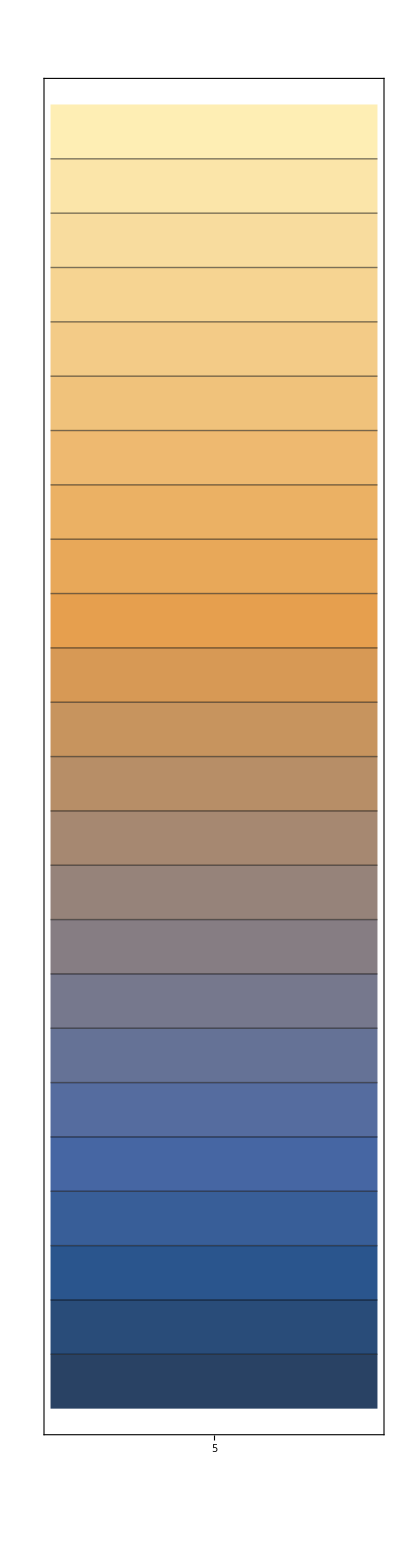
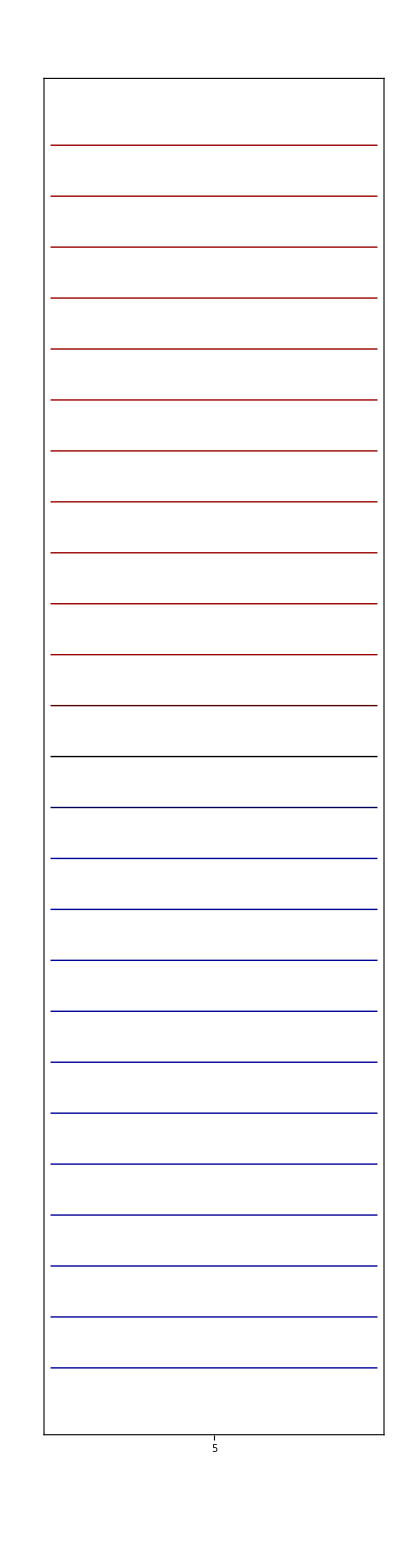

```mathematica
Row[Show[#,ImageSize->{{300},{250}}]&/@{
figure5DReLabel=cleanContourPlot@ContourPlot[y,{x,0,1},{y,0,120}
,Contours->Range[0,120,5]
,PlotRangePadding->None
,ImagePadding->{{0.5,18},{3,3}}
,AspectRatio->9
,ImageSize->{{600},{49}}
,ColorFunction->contourPlotReColorFunction
,BaseStyle->{{FontFamily->"Latin Modern Math"}}
,FrameTicks->{{None,{#,Style[ToString[#],7],{0,0.3}}&/@Range[0,120,30]},{{{0.5,Style["5",Opacity[0]],{0,0}}},None}}
],
figure5DImLabel=cleanContourPlot@ContourPlot[y,{x,0,1},{y,-64,64}
,Contours->Range[-60,60,5]
,ContourShading->None
,PlotRangePadding->None
,ContourStyle->(contourPlotImColorFunction[#/9]&/@Range[-60,60,5])
,ImagePadding->{{0.5,18},{2,2}}
,AspectRatio->9
,ImageSize->{{600},{49}}
,BaseStyle->{{FontFamily->"Latin Modern Math"}}
,FrameTicks->{{None,{#,Style[ToString[#],7],{0,0.3}}&/@Range[-60,60,30]},{{{0.5,Style["5",Opacity[0]],{0,0}}},None}}
]
}]
```

#### Figure 5Da

```mathematica
DateString[]
Block[{
F,ω,κ,po,py,pp,rules,tss,r2,Tend="T",plotter
},
{F,ω,κ}=figure5Dparameters;
{po,py,pp}=figure5Dmomentum;

tss=ts[pp,κ,ω,F,po,py];
rules={"tκ"->tss-ⅈ/κ^2,"ts"->tss,"t0"->Re[tss],"τ"->Im[tss],"T"-> 2π/ω};
r2[tt_]:=(po(tt-tss))^2+py^2(tt-tss)^2+(pp(tt-tss)+F/ω^2(Cos[ω tt]-Cos[ω tss]))^2;

plotter[part_,contours_,opts:OptionsPattern[{}]]:=ContourPlot[
part[√r2[(reωt+ⅈ imωt)/ω]]
,{reωt,-1ω,ω(Re[Tend]+10/.rules)},{imωt,-10ω,ω Max[Im[tss]+10,15]}
,AspectRatio->Automatic,AxesOrigin->{0,0},PlotRangePadding->0
,ImageSize->390
,Contours->contours
,Axes->False
,ContourShading->Evaluate[part/.{Re->True,Im->False}]
,ColorFunction->Evaluate[If[part===Im,Opacity[0]&,contourPlotReColorFunction]]
(*,ContourStyle->If[part===Re,{{Black,Thickness[0.0025]}},{{Blend[{RGBColor[0.1,0.1,1],Black,RGBColor[0.9,0,0]},1/2+contours⟦1⟧/(2 9)],Thickness[0.0025]}}]*)
,ContourStyle->If[part===Re,{{Black,Thickness[0.0025]}},{{Blend[{RGBColor[0,0,0.6],Black,RGBColor[0.6,0,0]},1/2+contours⟦1⟧/(2 9)],Thickness[0.0025]}}]
,BaseStyle->{{FontFamily->"Latin Modern Math"}}
,FrameTicks->{
{
Join[{#,MaTeX[ToString[PaddedForm[#,{2,1}]],FontSize->9]}&/@Range[-2,2,0.5],{#,"",{0.005,0}}&/@Range[-2,2,0.1]],
Join[{#,""}&/@Range[-2,2,1],{#,"",{0.005,0}}&/@Range[-2,2,0.1]]
},{
Join[
{# π,MaTeX[StringReplace[ToString[Numerator[#]]<>"\\pi/"<>ToString[Denominator[#]],{"/1"->"","1\\pi"->"\\pi","0\\pi"->"0"}],FontSize->9]}&/@Range[0,2,1/4],
({#,"",{0.005,0}}&/@Range[0,4π,π/16])],
Join[({# π,"",{0.010,0}}&/@Range[0,8,1/4]),({#,"",{0.005,0}}&/@Range[0,4π,π/16])]
}}
,FrameLabel->{MaTeX["\\mathrm{Re}(\\omega t)",FontSize->9],MaTeX["\\mathrm{Im}(\\omega t)",FontSize->9]}
];
AbsoluteTiming[
figure5Da=Show[{
cleanContourPlot[plotter[Re,Range[-120,120,5]]]
}~Join~Table[
plotter[Im,{c}]
,{c,Range[-120,120,5]}]~Join~{
Graphics[{PointSize[Large],Purple,Point[{Re[ω"ts"],Im[ω"ts"]}/.rules]}],
Graphics[Inset[MaTeX["\\color[gray]{0.8}{t_s}",FontSize->9],({Re[ω"ts"],Im[ω"ts"]}/.rules)+{0.1,-0.25},Scaled[{0,0.9}]]],
Graphics[{Thickness[0.001],GrayLevel[0.8],Arrowheads[0.010],Arrow[{{Re[ω"ts"],Im[ω"ts"]}+{0.1,-0.25},{Re[ω"ts"],Im[ω"ts"]}}/.rules,ω{0,1}]}],

Graphics[Inset[figure5DImLabel,Scaled[{1.02,0}],Scaled[{0,0}]]],
Graphics[Inset[figure5DReLabel,Scaled[{1.02,1}],Scaled[{0,1}]]],
Graphics[Inset[Rotate[MaTeX["\\mathrm{Re}\\mathopen{}\\left(\\sqrt{\\mathbf r_\\mathrm{L}(t)^2}\\right)\\mathclose{}",FontSize->9,Magnification->0.7],90°],Scaled[{1.105,0.75}],Scaled[{0.5,0.5}]]],
Graphics[Inset[Rotate[MaTeX["\\mathrm{Im}\\mathopen{}\\left(\\sqrt{\\mathbf r_\\mathrm{L}(t)^2}\\right)\\mathclose{}",FontSize->9,Magnification->0.7],90°],Scaled[{1.105,0.25}],Scaled[{0.5,0.5}]]],

Graphics[Inset[MaTeX["\\mathrm{(a)}",FontSize->9],Scaled[{-0.06,1}],Scaled[{1,1}]]]
}
,ImageSize->415
,PlotRangeClipping->False
,PlotRange->All
,ImagePadding->{{35,43},{35,3}}
];
]
]
figure5Da
DateString[]
(*Show[ColorConvert[figure5a,"Grayscale"],ImageSize->700]*)
FileByteCount[Export[$OutputDirectory<>"figure5Da.pdf",figure5Da,Background->None]]
```

Mon 24 Oct 2016 21:13:37

{22.3978,Null}

Mon 24 Oct 2016 21:14:00

165402

#### Figure 5Db

```mathematica
figure5DbLabelsPlotter[path_,rules_,OptionsPattern[{"root"->None}]]:=Show[{
Graphics[Inset[MaTeX["t_s",FontSize->9],{Re["ts"],Im["ts"]}+5{1,1}/.rules,Scaled[{0,0.25}]]],
Graphics[{Thickness[0.001],Arrowheads[0.015],Arrow[{{Re["ts"],Im["ts"]}+5{1,1},{Re["ts"],Im["ts"]}}/.rules,{0,1}]}],

Graphics[Inset[MaTeX["t_\\kappa",FontSize->9],{Re["tκ"],Im["tκ"]}+5{1,-1}/.rules,Scaled[{0,0.8}]]],
Graphics[{Thickness[0.001],Arrowheads[0.015],Arrow[{{Re["tκ"],Im["tκ"]}+5{1,-1},{Re["tκ"],Im["tκ"]}}/.rules,{0,1}]}],

Graphics[Inset[MaTeX["t_0",FontSize->9],{Re["t0"],Im["t0"]}+5{1,1}/.rules,Scaled[{0,0.25}]]],
Graphics[{Thickness[0.001],Arrowheads[0.015],Arrow[{{Re["t0"],Im["t0"]}+5{1,1},{Re["t0"],Im["t0"]}}/.rules,{0,1}]}],

Graphics[Inset[MaTeX["T",FontSize->9],{Re[Last[path]],Im[Last[path]]}+5{-1,1}/.rules,Scaled[{0.85,0.25}]]],
Graphics[{Thickness[0.001],Arrowheads[0.015],Arrow[{{Re[Last[path]],Im[Last[path]]}+5{-1,1},{Re[Last[path]],Im[Last[path]]}}/.rules,{0,1}]}],

Sequence@@If[(OptionValue["root"])===None,##&[],{
Graphics[Inset[MaTeX["t_{\\scriptscriptstyle\\mathrm{CA}}",FontSize->9],{Re[OptionValue["root"]],Im[OptionValue["root"]]}+{-5,4}/.rules,Scaled[{1,0.25}]]],
Graphics[{Thickness[0.001],Arrowheads[0.015],Arrow[{{Re[OptionValue["root"]],Im[OptionValue["root"]]}+{-5,4},{Re[OptionValue["root"]],Im[OptionValue["root"]]}},{0,0.75}]}]
}]
}]
```

```mathematica
figure5Db=Block[{
F,ω,κ,po,py,pp,rules,tss,r2,rv,root,path,t,tmod
},
{F,ω,κ}=figure5Dparameters;
{po,py,pp}=figure5Dmomentum;

tss=ts[pp,κ,ω,F,po,py];
rules={"tκ"->tss-ⅈ/κ^2,"ts"->tss,"t0"->Re[tss],"τ"->Im[tss],"T"-> 2π/ω};
r2=(po(tt-tss))^2+py^2(tt-tss)^2+(pp(tt-tss)+F/ω^2(Cos[ω tt]-Cos[ω tss]))^2;

path={"t0","T"}/.rules;

t=Interpolation[Evaluate[{Range[0,1,1/(Length[path]-1)],path}ᵀ],InterpolationOrder->1];

rv[ret_,imt_]:=(D[r2,tt]/.{tt->ret+ⅈ imt});

root=((ret+ⅈ imt)/.FindRoot[{Re[rv[ret,imt]],Im[rv[ret,imt]]},{{ret,80},{imt,3}}]);

tmod=Interpolation[Evaluate[{Range[0,1,1/3],{"tκ","t0",root,Last[path]}/.rules}ᵀ],InterpolationOrder->1];
Show[{
timeContours[r2,rules,tss,path,{{-1,All},{All,All}},PlotPoints->50,"root"->root],
timePathPlotter[rules,t,PlotStyle->{Blue,Dashing[{0,0.025}]},showstart->False],
timePathPlotter[rules,tmod],
figure5DbLabelsPlotter[path,rules,"root"->root],
Graphics[Inset[MaTeX["\\mathrm{(b)}",FontSize->9],Scaled[{-0.06,1}],Scaled[{1,1}]]],

Graphics[{(*To stop line leakage*)
White,EdgeForm[None],
Rectangle[{-1.5,20},{-1,30}],
Rectangle[{70,-10.5},{90,-10}],
Rectangle[{80,31.09},{100,32}],
Rectangle[{10,31.09},{30,32}]
}]
}
,ImageSize->415
,ImagePadding->{{35,43},{35,3}}
,PlotRangeClipping->False
]
]
FileByteCount[Export[$OutputDirectory<>"figure5Db.pdf",Show[figure5Db],Background->None]]
```

39010

#### Figure 5D export

```mathematica
FileByteCount[Export[$OutputDirectory<>"figure5Da.pdf",figure5Da,Background->None]]
FileByteCount[Export[$OutputDirectory<>"figure5Db.pdf",figure5Db,Background->None]]
Export[$OutputDirectory<>"Figure5DParameters.tex",StringJoin[
"\\newcommand{\\figurefiveDpo}{",ToString[NumberForm[figure5Dmomentum⟦1⟧,2]],"} \n",
"\\newcommand{\\figurefiveDpp}{",ToString[NumberForm[figure5Dmomentum⟦3⟧,2]],"}"
],"Text"];
```

164386

39053

### Figure 5F - zoom in to first branch cut gate

#### Figure 5F label

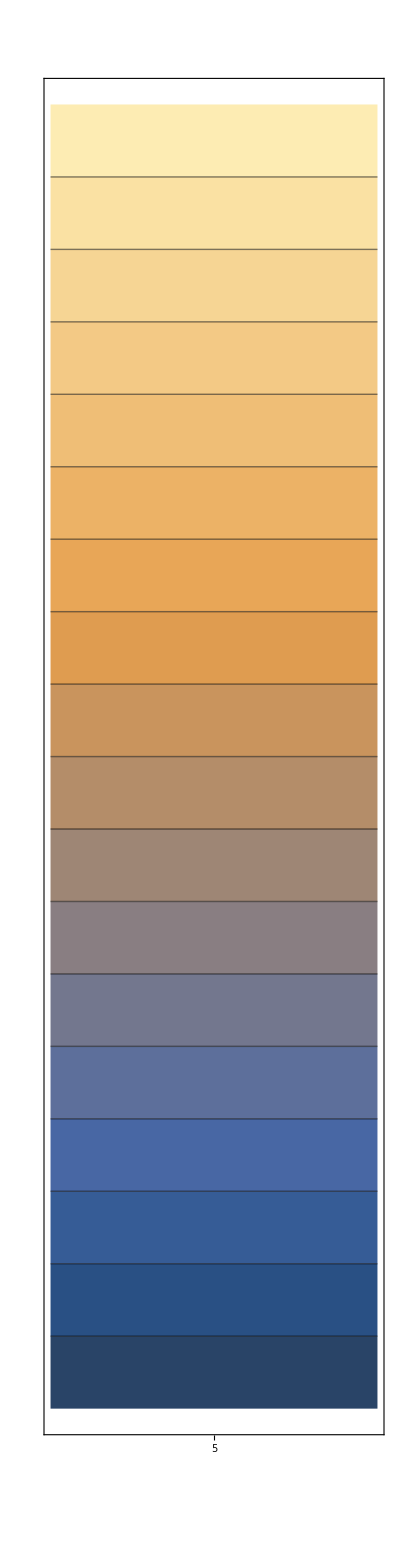
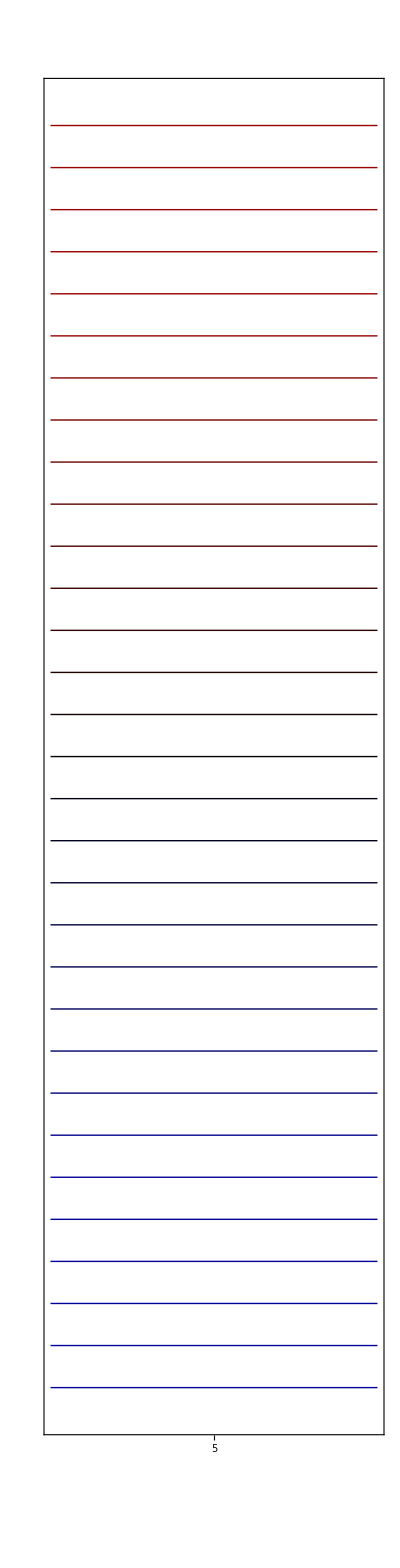

```mathematica
Row[Show[#,ImageSize->{{300},{250}}]&/@{
figure5FReLabel=cleanContourPlot@ContourPlot[y,{x,0,1},{y,0,3.6}
,Contours->Range[0,3.6,0.2]
,PlotRangePadding->None
,ImagePadding->{{0.5,13},{2.5,2}}
,AspectRatio->9
,ImageSize->{{600},{80}}
,ColorFunction->contourPlotReColorFunction
,BaseStyle->{{FontFamily->"Latin Modern Math"}}
,FrameTicks->{{None,{#,Style[ToString[#],7],{0,0.3}}&/@Range[0,3.6,1]},{{{0.5,Style["5",Opacity[0]],{0,0}}},None}}
],
figure5FImLabel=cleanContourPlot@ContourPlot[y,{x,0,1},{y,-3.1,3.1}
,Contours->Range[-3,3,0.2]
,ContourShading->None
,PlotRangePadding->None
,ContourStyle->(contourPlotImColorFunction[#/2]&/@Range[-3,3,0.2])
,ImagePadding->{{0.5,13},{2,2}}
,AspectRatio->9
,ImageSize->{{600},{80}}
,BaseStyle->{{FontFamily->"Latin Modern Math"}}
,FrameTicks->{{None,{#,Style[ToString[#],7],{0,0.3}}&/@Range[-2,2,2]},{{{0.5,Style["5",Opacity[0]],{0,0}}},None}}
]
}]
```

#### Figure 5F

```mathematica
Block[{
F,ω,κ,po,py,pp,rules,tss,r2,Tend="T",plotter,rv,root
},
{F,ω,κ}=figure5Dparameters;
{po,py,pp}=figure5Dmomentum;

tss=ts[pp,κ,ω,F,po,py];
rules={"tκ"->tss-ⅈ/κ^2,"ts"->tss,"t0"->Re[tss],"τ"->Im[tss],"T"-> 2π/ω};
r2[tt_]:=(po(tt-tss))^2+py^2(tt-tss)^2+(pp(tt-tss)+F/ω^2(Cos[ω tt]-Cos[ω tss]))^2;

rv[ret_,imt_]:=(D[r2[tt],tt]/.{tt->ret+ⅈ imt});

root=((ret+ⅈ imt)/.FindRoot[{Re[rv[ret,imt]],Im[rv[ret,imt]]},{{ret,78},{imt,3}}]);

plotter[part_,contours_]:=ContourPlot[
part[√r2[(reωt+ⅈ imωt)/ω]]
,{reωt,3.45,3.65},{imωt,0.05,0.25}

(*,PlotPoints->5*)

,AspectRatio->Automatic,AxesOrigin->{0,0},PlotRangePadding->0
,Contours->contours
,Axes->False
,ContourShading->Evaluate[part/.{Re->True,Im->False}]
,ColorFunction->contourPlotReColorFunction
,ContourStyle->If[part===Re,Black,contourPlotImColorFunction[contours⟦1⟧/2]]
,BaseStyle->{FontFamily->"Latin Modern Math"}
,FrameLabel->{MaTeX["\\mathrm{Re}(\\omega t)",FontSize->9],MaTeX["\\mathrm{Im}(\\omega t)",FontSize->9]}
,FrameTicks->{
{
Join[{#,MaTeX[ToString[PaddedForm[#,{3,2}]],FontSize->9]}&/@Range[0.05,0.25,0.05],{#,"",{0.008,0}}&/@Range[0.05,0.25,0.01]],
Join[{#,""}&/@Range[0.05,0.25,0.05],{#,"",{0.008,0}}&/@Range[0.05,0.25,0.01]]
},{
Join[
{# π,MaTeX[ToString[PaddedForm[#,{3,2}]]<>"\\pi",FontSize->9]}&/@Range[1.1,1.16,0.02],
({# π,"",{0.008 ,0}}&/@Range[1,1.18,0.004])],
Join[({# π,"",{0.010,0}}&/@Range[1.1,1.16,0.02]),({# π,"",{0.008 ,0}}&/@Range[1,1.18,0.004])]
}}
];

figure5F=Show[{
cleanContourPlot[plotter[Re,Range[-4,4,0.2]]]
}~Join~Table[
plotter[Im,{c}]
,{c,Range[-4,4,0.2]}]~Join~{
Graphics[{PointSize[0.03],Darker[Gray],Point[{Re[ω #],Im[ω#]}&[root]]}],
Graphics[Inset[MaTeX["t_{\\scriptscriptstyle \\mathrm{CA}}",FontSize->11],{Re[ω#],Im[ω#]}&[root]+ω{-0.72,0.12},Scaled[{1,0.3}]]],
(*Graphics[Text[Style[TraditionalForm["t_CA"],12,FontWeight->"Thin"],{Re[ω#],Im[ω#]}&[root]+ω{-0.72,0.12},{1,0}]],*)
Graphics[{Thickness[0.002],Arrowheads[0.040],Arrow[{{Re[ω#],Im[ω#]}&[root]+ω{-0.72,0.12},{Re[ω#],Im[ω#]}&[root]},ω{0,0.1}]}],


Graphics[Inset[figure5FImLabel,Scaled[{1.08,0}],Scaled[{0,0}]]],
Graphics[Inset[figure5FReLabel,Scaled[{1.08,1}],Scaled[{0,1}]]],
Graphics[Inset[Rotate[MaTeX["\\mathrm{Re}\\mathopen{}\\left(\\!\\!\\sqrt{\\mathbf r_\\mathrm{L}(t)^2}\\right)\\mathclose{}",FontSize->9,Magnification->0.9],90°],Scaled[{1.28,0.75}],Scaled[{0.5,0.5}]]],
Graphics[Inset[Rotate[MaTeX["\\mathrm{Im}\\mathopen{}\\left(\\!\\!\\sqrt{\\mathbf r_\\mathrm{L}(t)^2}\\right)\\mathclose{}",FontSize->9,Magnification->0.9],90°],Scaled[{1.28,0.25}],Scaled[{0.5,0.5}]]]
}
,ImageSize->250
,ImagePadding->{{40,55},{35,5}}
,PlotRangeClipping->False
]
]/.{EdgeForm[],r_?(MemberQ[{RGBColor,Hue,CMYKColor,GrayLevel},Head[#]]&),i___}:>{EdgeForm[r],r,i}
(*Show[ColorConvert[%,"Grayscale"]]*)
FileByteCount[Export[$OutputDirectory<>"figure5F.pdf",figure5F,Background->None]]
```

103832

```mathematica
FileByteCount[Export[$OutputDirectory<>"figure5F.pdf",figure5F,Background->None]]
```

```mathematica
{3.45,3.65}/π
```

{1.09817,1.16183}

### Figure 5H - trajectories

#### Figure 5H

```mathematica
figure5Hparameters=onemicronpars;
```

```mathematica
Block[{F,ω,κ,plotter,fs=9,arrowmaker,arrow,arrsize,arr,txt},
{F,ω,κ}=figure5Hparameters;
plotter[pxr_,pzr_,opts:OptionsPattern[{"tEnd"->"T",PlotRange->Automatic}]]:=Show[{
ParametricPlot[
{#1,#3}&@@classicalTrajectory[t,F/ω{pxr,0,pzr},{F,ω,κ}]
,{t,t0[F/ω{pxr,0,pzr},{F, ω, κ}],OptionValue["tEnd"]/.{"T"->2π/ω}}
,Evaluate[Sequence@@FilterRules[{opts},ParametricPlot]]
,PlotRangeClipping->True
,Frame->True,Axes->False
(*Method->{"AxesInFront"->False},AxesStyle->GrayLevel[0.8],AxesOrigin->{0,0}*)
,PlotRangePadding->None
,PlotStyle->{Blue,AbsoluteThickness[1]}
,AspectRatio->Automatic
,RegionFunction->Function[{x,y,t},OptionValue[PlotRange]⟦1,1⟧<x<OptionValue[PlotRange]⟦1,2⟧&&OptionValue[PlotRange]⟦2,1⟧<y<OptionValue[PlotRange]⟦2,2⟧]
]
}~Join~(
Graphics[
{GrayLevel[0.4],AbsolutePointSize[4],Point[classicalTrajectory[#,F/ω{pxr,0,pzr},{F,ω,κ}]⟦{1,3}⟧]}
]&/@classicalClosestApproach[F/ω{pxr,0,pzr},{F,ω,κ},"Range"->{0,OptionValue["tEnd"]}]
)];
arrsize=0.5;
arrow=Graphics[Polygon[{{0,0},Offset[arrsize{-10,3},{0,0}],Offset[arrsize{-8,0},{0,0}],Offset[arrsize{-10,-3},{0,0}]}]];
arrowmaker[pxr_,pzr_,t_,txt_,offset_:{0.3,0.05}]:=Sequence[
Graphics[{AbsoluteThickness[0.5],Arrowheads[{{0.1,1,arrow}}],Arrow[{(arr=classicalTrajectory[t,F/ω{pxr,0,pzr},{F,ω,κ}]⟦{1,3}⟧)+txt,arr},offset]}],
Graphics[Text[Style["("<>ToString[pxr]<>", "<>ToString[pzr]<>")",10],arr+txt]]
];

figure5Ha=Show[{
Graphics[{GrayLevel[0.8],Line[{{0,-56},{0,23}}],Line[{{-3,0},{35,0}}]}],
plotter[0.15,0.05,"tEnd"->1.45"T",PlotRange->{{-3,35},{-56,23}}],
plotter[0.15,0.20,"tEnd"->1.45"T",PlotRange->{{-3,35},{-56,23}}],
arrowmaker[0.15,0.05,102,{7.5,-22.5},{3,0.75}],
arrowmaker[0.15,0.20,93,{-7.5,22.5},{3,0.75}]
}
,ImageSize->{{5000},(sa=0.58){s0=400}}
,PlotRange->{{-3,35},{-56,23}}
,ImagePadding->{{Scaled[0.065],Scaled[0.00001]}, {Scaled[0.023], Scaled[0.00001]}}
,Frame->True
,PlotRangeClipping->False
,BaseStyle->{FontFamily->"Latin Modern Math"}
,FrameTicks->{Transpose[{{#,Style[ToString[#],fs]},{#,""}}&/@Range[-60,60,10]],Transpose[{{#,Style[ToString[#],fs]},{#,""}}&/@Range[0,35,10]]}
,Epilog->{
Inset[Style["(a)",11],Scaled[{0.12,0.96}],Scaled[{0,1}]],
Inset[Rotate[MaTeX["z \\ \\mathrm{(a.u.)}",FontSize->10],90°],ImageScaled[{0,0.55}],Scaled[{0,0.5}]]
}
];
figure5Hb=Show[{
Graphics[{GrayLevel[0.8],Line[{{0,-13},{0,0.5}}],Line[{{-0.5,0},{10,0}}]}],
plotter[0.2,0.95,"tEnd"->0.5"T",PlotRange->{{-0.5,10},{-13,0.5}}],
plotter[0.2,1.05,"tEnd"->0.5"T",PlotRange->{{-0.5,10},{-13,0.5}}],
plotter[0.2,1.15,"tEnd"->0.5"T",PlotRange->{{-0.5,10},{-13,0.5}}],
arrowmaker[0.2,1.15,35,1.2{-1,1.5},{0.4,0.07}],
arrowmaker[0.2,0.95,35,1.2{-0.5,-1.5},{0.4,0.07}]
}
,ImageSize->{{5000},(sb=sa){s0}}
,PlotRange->{{-0.5,10},{-13,0.5}}
,ImagePadding->{{Scaled[0.038],Scaled[0.00001]}, {Scaled[0.023], Scaled[0.00001]}}
,FrameLabel->{None,None}
,Frame->True
,PlotRangeClipping->True
,BaseStyle->{FontFamily->"Latin Modern Math"}
,FrameTicks->{Transpose[{{#,Style[ToString[#],fs]},{#,""}}&/@Range[-14,0,2]],Transpose[{{#,Style[ToString[#],fs]},{#,""}}&/@Range[0,8,2]]}
,Epilog->Inset[Style["(b)",11],Scaled[{0.08,0.96}],Scaled[{0,1}]]
];
figure5Hc=Show[{
Graphics[{GrayLevel[0.8],Line[{{0,-170},{0,3}}],Line[{{-3,0},{50,0}}]}],
plotter[0.3,-0.8,"tEnd"->1.1"T",PlotRange->{{-3,50},{-170,3}}],
plotter[0.3,-0.9,"tEnd"->1.1"T",PlotRange->{{-3,50},{-170,3}}],
plotter[0.3,-1.0,"tEnd"->1.1"T",PlotRange->{{-3,50},{-170,3}}],
arrowmaker[0.3,-0.8,72,1.2{7,15},{2,0.5}],
arrowmaker[0.3,-1,60,1.2{-7,-15},{2,0.5}]
}
,ImageSize->{{5000},(sc=1){s0}}
,PlotRange->{{-3,50},{-170,3}}
,ImagePadding->{{Scaled[0.05],Scaled[0.008]}, {Scaled[0.05], Scaled[0.00001]}}
,Frame->True
,PlotRangeClipping->False
,BaseStyle->{FontFamily->"Latin Modern Math"}
,FrameTicks->{Transpose[{{#,Style[ToString[#],fs]},{#,""}}&/@Range[-150,0,30]],Transpose[{{#,Style[ToString[#],fs]},{#,""}}&/@Range[0,50,10]]}
,Epilog->{
Inset[Style["(c)",11],Scaled[{0.10,0.98}],Scaled[{0,1}]],
Inset[MaTeX["x \\ \\mathrm{(a.u.)}",FontSize->10],ImageScaled[{0.65,0.0}],Scaled[{0.5,0}]]
}
];
figure5Hd=Show[{
Graphics[{GrayLevel[0.8],Line[{{0,-24},{0,-8}}]}],
plotter[0.4,0.6,"tEnd"->0.6"T",PlotRange->{{-1,34},{-24,-8}}],
plotter[0.45,0.6,"tEnd"->0.6"T",PlotRange->{{-1,34},{-24,-8}}],
arrowmaker[0.4,0.6,29.5/.8,2{-2,-1.5},{1.1,0.15}],
arrowmaker[0.45,0.6,28/.8,2{2,1.5},{0.9,0.15}]
}
,ImageSize->{{5000},(sd=1-sa){s0}}
,PlotRange->{{-1,34},{-24,-8}}
,ImagePadding->{{Scaled[0.065],Scaled[0.00001]}, {Scaled[0.05], Scaled[0.01]}}
,Frame->True
,PlotRangeClipping->False
,BaseStyle->{FontFamily->"Latin Modern Math"}
,FrameTicks->{Transpose[{{#,Style[ToString[#],fs]},{#,""}}&/@Range[-30,0,5]],Transpose[{{#,Style[ToString[#],fs]},{#,""}}&/@Range[0,40,5]]}
,Epilog->{
Inset[Style["(d)",11],Scaled[{0.06,0.98}],Scaled[{0,1}]],
Inset[Rotate[MaTeX["z\\ \\mathrm{(a.u.)}",FontSize->10],90°],ImageScaled[{0,0.6}],Scaled[{0,0.5}]],
Inset[MaTeX["x \\ \\mathrm{(a.u.)}",FontSize->10],ImageScaled[{0.6,0.0}],Scaled[{0.5,0}]]
}
];
Row[{Column[{Row[{figure5Ha,figure5Hb}],figure5Hd}],figure5Hc}];
]
stot=s0;
figure5H=Row[{
Column[{
Row[{
Show[figure5Ha,ImageSize->{{5000},{sa stot}}],Spacer[4],
Show[figure5Hb,ImageSize->{{5000},{sb stot}}]
}],
Show[figure5Hd,ImageSize->{{5000},{sd stot}}]
},Spacings->0,BaselinePosition->Bottom],
Spacer[5],
Column[{
Show[figure5Hc,ImageSize->{{5000},{sc stot+1}}]
},BaselinePosition->Bottom]
},Alignment->{Left,Bottom}];
Export[
$OutputDirectory<>"figure5H.pdf",
figure5H
,Background->None
];
```

#### Dynamical trajectory mapper

```mathematica
DynamicModule[{F,ω,κ,plotter,px=0.1,pz=0.6},
{F,ω,κ}=figure5Hparameters;
plotter[px_,pz_,opts:OptionsPattern[{"tEnd"->"T"}]]:=Show[{
ParametricPlot[
{#1,#3}&@@classicalTrajectory[t,F/ω{px,0,pz},{F,ω,κ}]
,{t,t0[F/ω{px,0,pz},{F, ω, κ}],OptionValue["tEnd"]/.{"T"->2π/ω}}
,Evaluate[Sequence@@FilterRules[{opts},ParametricPlot]]
,Frame->True,Axes->False(*True,Method->{"AxesInFront"->False},AxesStyle->GrayLevel[0.8],AxesOrigin->{0,0}*)
,PlotStyle->{Blue}
,AspectRatio->Automatic
]
}~Join~(
Graphics[
{GrayLevel[0.4],PointSize[0.03],Point[classicalTrajectory[#,F/ω{px,0,pz},{F,ω,κ}]⟦{1,3}⟧]}
]&/@classicalClosestApproach[F/ω{px,0,pz},{F,ω,κ},"Range"->{0,OptionValue["tEnd"]}]
)];
Row[{
Dynamic[LocatorPane[Dynamic[{px,pz}],Show[Graphics[],ImageSize->250,Frame->True,Axes->True,PlotRange->{{-1,1},{-1.5,1.5}}]]],
Dynamic[{px,pz}],
Show[plotter[0.1,0.7,"tEnd"->"T"/2],ImageSize->{{400},{300}}]
}]
]
```

### Figure 5K - soft recollision before & after

#### Parameters

```mathematica
figure5Kmomenta={0.001,0.063,0.0635}; (*  {po, F ppl/ω, F pph/ω}  *)
figure5Kparameters=onemicronpars;
```

#### Figure 5K labels

```mathematica
Block[{fs=6.5},
labelheight=51;
Row[{figure5KRerLabel=cleanContourPlot@ContourPlot[y,{x,0,1},{y,0,0.8}
,Contours->Range[0,0.8,0.1]
,PlotRangePadding->None
,ImagePadding->{{0.5,20},{3,2}}
,AspectRatio->9
,ImageSize->{{600},{labelheight}}
,ColorFunction->contourPlotReColorFunction
,FrameTicks->{{None,{#,Style[ToString[PaddedForm[#,{2,1}]],fs],{0,0.3}}&/@Range[0,0.8,0.2]},{None,None}}
],
figure5KImrLabel=cleanContourPlot@ContourPlot[y,{x,0,1},{y,-1.65,1.65}
,Contours->Range[-1.7,1.7,0.1]
,ContourShading->None
,PlotRangePadding->None
,ContourStyle->(contourPlotImColorFunction[Quiet@Interpolation[{{-1.6,-1.6},{1.6,1.6}},InterpolationOrder->1][#]]&/@Range[-1.7,1.7,0.1])
,ImagePadding->{{0.5,20},{2,2}}
,AspectRatio->9
,ImageSize->{{600},{labelheight}}
,FrameTicks->{{None,{#,Style[ToString[PaddedForm[#,{2,1}]],fs],{0,0.3}}&/@Range[-1.6,1.6,0.8]},{None,None}}
],
figure5KRev2Label=cleanContourPlot@ContourPlot[y,{x,0,1},{y,-0.065,0.065}
,Contours->Range[-0.06,0.06,0.02]
,PlotRangePadding->None
,ImagePadding->{{0.5,22},{1,2}}
,AspectRatio->9
,ImageSize->{{600},{labelheight}}
,ColorFunction->contourPlotReColorFunction
,FrameTicks->{{None,{#,Style[ToString[PaddedForm[#,{3,2}]],fs],{0,0.3}}&/@Range[-0.04,0.04,0.04]},{None,None}}
,ContourStyle->{{Black},{Black},{Black},{Black,Thick},{Black},{Black},{Black}}
,PlotRangeClipping->True
],
figure5KImv2Label=cleanContourPlot@ContourPlot[y,{x,0,1},{y,-0.145,0.145}
,Contours->Range[-0.14,0.14,0.02]
,ContourShading->None
,PlotRangePadding->None
,ContourStyle->(contourPlotImColorFunction[Interpolation[{{-0.14,-1.6},{0.14,1.6}},InterpolationOrder->1][#],1]&/@Range[-0.14,0.14,0.02])
,ImagePadding->{{0.5,22},{1,2}}
,AspectRatio->9
,ImageSize->{{600},{labelheight}}
,FrameTicks->{{None,{#,Style[ToString[PaddedForm[#,{3,2}]],fs],{0,0.3}}&/@Range[-0.12,0.12,0.06]},{None,None}}
]}]
];
```

#### Figure 5K - topology of the transition

```mathematica
Column@AbsoluteTiming@Block[
{F,ω,κ,po,py,ppl,pph,rules,tss,r,v2,plotter,subplotter,centre,s=0.26,txt,gray},
{F,ω,κ}=figure5Kparameters;
py=0;{po,ppl,pph}={#1,F/ω#2,F/ω#3}&@@figure5Kmomenta;
centre=First[Re[ω tCA]/.allQuantumClosestApproachTimes[{po,py,ppl},{F,ω,κ},{0,0,0},"Range"->(2 π+0.05+0.05{-1-ⅈ,1+ⅈ})/ω]];
subplotter[f_,pp_,part_,contours_,options:OptionsPattern[
Join[{"LeftPadding"->Automatic,"RightPadding"->10,"BottomPadding"->Automatic,"TopPadding"->2.5,"contourscaler"->Function[x,(1+x)/2],"PlotPoints"->10,"LeftTicks"->Automatic},Options[ContourPlot]]]
]:=(
tss=ts[pp,κ,ω,F,po,py];
rules={"tκ"->tss-ⅈ/κ^2,"ts"->tss,"t0"->Re[tss],"τ"->Im[tss],"T"-> 2π/ω};
r[tt_]:=√((po(tt-tss))^2+py^2(tt-tss)^2+(pp(tt-tss)+F/ω^2(Cos[ω tt]-Cos[ω tss]))^2);
v2[tt_]:=po^2+py^2+(pp-F/ω Sin[ω tt])^2;
ContourPlot[
part[f[(reωt+ⅈ imωt)/ω]]
,{reωt,centre-s,centre+s},{imωt,-s,s}
,Evaluate[Sequence@@FilterRules[{options},Options[ContourPlot]]]
,AspectRatio->Automatic,AxesOrigin->{0,0},PlotRangePadding->0
,ImageSize->{{600},{290}}
,PlotPoints->OptionValue["PlotPoints"]
,Contours->contours
,Axes->False
,ContourShading->Evaluate[part/.{Re->True,Im->False}]
,ContourStyle->If[part===Re,Black,contourPlotImColorFunction[OptionValue["contourscaler"][contours⟦1⟧]],1]
,ColorFunction->contourPlotReColorFunction
,ImagePadding->{{OptionValue["LeftPadding"],OptionValue["RightPadding"](*3*)},{OptionValue["BottomPadding"],OptionValue["TopPadding"]}}
,BaseStyle->{FontFamily->"Latin Modern Math"}
,FrameTicks->{{
Join[{#,If[OptionValue["LeftTicks"]===Automatic,MaTeX[ToString[PaddedForm[#,{2,1}]],FontSize->7],""],{0.03,0}}&/@Chop[Range[-0.3,0.3,0.1]],{#,"",{0.015,0}}&/@Range[-0.3,0.3,0.02]],
Join[{#,"",{0.03,0}}&/@Chop[Range[-0.3,0.3,0.1]],{#,"",{0.015,0}}&/@Range[-0.3,0.3,0.02]]
},{
Join[{# π,MaTeX[ToString[PaddedForm[#,{3,2}]]<>"\\pi",FontSize->7],{0.03,0}}&/@Range[1.95,2.1,0.05],{# π,"",{0.015,0}}&/@Range[1.9,2.1,0.01]],
Join[{# π,"",{0.03,0}}&/@Range[1.95,2.1,0.05],{# π,"",{0.015,0}}&/@Range[1.9,2.1,0.01]]
}}
]);
plotter[f_,pp_,ReRange_,ImRange_,options:OptionsPattern[Join[{"LeftPadding"->Automatic,"RightPadding"->Automatic,"BottomPadding"->Automatic,"BottomLabel"->"Re(ωt)","LeftTicks"->Automatic,"TopPadding"->2.5},Options[ContourPlot]]]]:=Show[{
cleanContourPlot[subplotter[f,pp,Re,ReRange,options]],
If[f===v2,
subplotter[f,pp,Re,{0},options,ContourShading->False,ContourStyle->{{Black,Thick}}]
,##&[]]
}~Join~Table[
subplotter[f,pp,Im,{c},"PlotPoints"->OptionValue["PlotPoints"],"contourscaler"->Interpolation[{{Min[ImRange],-1.6},{Max[ImRange],1.6}},InterpolationOrder->1]]
,{c,ImRange}]~Join~Table[
Show[
txt=Piecewise[{{{0.135,0},k==1},{{0.12,0},k==2},{{-0.135,0},k==3}}];
Graphics[{gray,PointSize[0.03],Point[{Re[ω tCA],Im[ω tCA]}]}],
Graphics[Inset[MaTeX["\\color[gray]{"<>ToString[gray⟦1⟧]<>"}{t_{\\scriptscriptstyle \\mathrm{CA}}^{("<>ToString[k]<>")} }",FontSize->9,Magnification->0.8],{Re[ω tCA],Im[ω tCA]}+txt]],
Graphics[{gray,Thickness[0.008],Arrowheads[0.035],Arrow[{{Re[ω tCA],Im[ω tCA]}+txt,{Re[ω tCA],Im[ω tCA]}},{0.03,0.015}]}]
]/.allQuantumClosestApproachTimes[{po,py,pp},{F,ω,κ},{0,0,0},"Range"->(2 π+0.1+s{-1-ⅈ,1+ⅈ})/ω]⟦k⟧,{k,1,3}]
,PlotRangeClipping->False
,Epilog->{Inset[Rotate[MaTeX["\\mathrm{Im}(\\omega t)",FontSize->9],90°],{centre-s-0.10,0},Scaled[{1,0.5}]]}
];
figure5Kheight=115;
figure5Kheight=125;
figure5KrightPadding=50;
{
gray=GrayLevel[0.8];
figure5Ka=Show[{
plotter[r,ppl,Range[0,0.8,0.1],Range[-1.6,1.6,0.1],ImageSize->{{500},{figure5Kheight}},"BottomPadding"->12,"LeftPadding"->Scaled[0.08],"TopPadding"->Scaled[0.03]],
Graphics[Inset[MaTeX["\\mathrm{(a)}\\ \\sqrt{\\mathbf{r}_\\mathrm{L}(t)^2}",FontSize->9,Magnification->0.9],Scaled[{0.5,1.0}],Scaled[{0.5,0}]]]
}]," ",
figure5Kb=Show[{
plotter[r,pph,Range[0,0.8,0.1],Range[-1.6,1.6,0.1],ImageSize->{{500},{figure5Kheight}},"RightPadding"->figure5KrightPadding,"BottomPadding"->12,"LeftPadding"->Scaled[0.008],"LeftTicks"->None,"TopPadding"->Scaled[0.03]],
Graphics[Inset[figure5KRerLabel,Scaled[{1.08,0}],Scaled[{0,0}]]],
Graphics[Inset[figure5KImrLabel,Scaled[{1.08,1}],Scaled[{0,1}]]],
Graphics[Inset[Rotate[MaTeX["\\mathrm{Re}",FontSize->9,Magnification->0.9],90°],Scaled[{1.4,0.75}],Scaled[{0.5,0.5}]]],
Graphics[Inset[Rotate[MaTeX["\\mathrm{Im}",FontSize->9,Magnification->0.9],90°],Scaled[{1.4,0.25}],Scaled[{0.5,0.5}]]],
Graphics[Inset[MaTeX["\\mathrm{(b)}\\ \\sqrt{\\mathbf{r}_\\mathrm{L}(t)^2}",FontSize->9,Magnification->0.9],Scaled[{0.5,1.0}],Scaled[{0.5,0}]]]
},PlotRangeClipping->False]," ",
gray=GrayLevel[0];
figure5Kc=Show[{
plotter[v2,ppl,Range[-0.06,0.06,0.02],Range[-0.14,0.14,0.02],ImageSize->{{500},{figure5Kheight}},"BottomPadding"->12,"LeftPadding"->Scaled[0.07],"PlotPoints"->30,"TopPadding"->Scaled[0.03]],
Graphics[Inset[MaTeX["\\mathrm{(c)}\\ \\mathbf{v}_\\mathrm{L}(t)^2",FontSize->9,Magnification->0.9],Scaled[{0.5,1.0}],Scaled[{0.5,0}]]]
}]," ",
figure5Kd=Show[{
plotter[v2,pph,Range[-0.06,0.06,0.02],Range[-0.14,0.14,0.02],ImageSize->{{500},{figure5Kheight}},"RightPadding"->figure5KrightPadding,"BottomPadding"->12,"LeftPadding"->Scaled[0.008],"LeftTicks"->None,"PlotPoints"->30,"TopPadding"->Scaled[0.03]],
Graphics[Inset[figure5KRev2Label,Scaled[{1.08,0}],Scaled[{0,0}]]],
Graphics[Inset[figure5KImv2Label,Scaled[{1.08,1}],Scaled[{0,1}]]],
Graphics[Inset[Rotate[MaTeX["\\mathrm{Re}",FontSize->9,Magnification->0.9],90°],Scaled[{1.4,0.75}],Scaled[{0.5,0.5}]]],
Graphics[Inset[Rotate[MaTeX["\\mathrm{Im}",FontSize->9,Magnification->0.9],90°],Scaled[{1.4,0.25}],Scaled[{0.5,0.5}]]],
Graphics[Inset[MaTeX["\\mathrm{(d)}\\ \\mathbf{v}_\\mathrm{L}(t)^2",FontSize->9,Magnification->0.9],Scaled[{0.5,1.0}],Scaled[{0.5,0}]]]
}]
};
]
Row[Style[#,Magnification->3]&/@{figure5Ka,figure5Kb,figure5Kc,figure5Kd}]
(*Show[ColorConvert[%,"Grayscale"]]*)
```

36.4075

```mathematica
TableForm[{StringSplit[#,"/"]⟦-1⟧,FileByteCount[#]}&/@{
Export[$OutputDirectory<>"figure5Ka.pdf",figure5Ka,Background->None],
Export[$OutputDirectory<>"figure5Kb.pdf",figure5Kb,Background->None],
Export[$OutputDirectory<>"figure5Kc.pdf",figure5Kc,Background->None],
Export[$OutputDirectory<>"figure5Kd.pdf",figure5Kd,Background->None]}]
Export[$OutputDirectory<>"Figure5KParameters.tex",StringJoin[
"\\newcommand{\\figurefiveKpo}{",ToString[#⟦1⟧],"}\n",
"\\newcommand{\\figurefiveKppl}{",ToString[#⟦2⟧],"}\n",
"\\newcommand{\\figurefiveKpph}{",ToString[#⟦3⟧],"}"
]&[figure5Kmomenta],"Text"];
```

figure5Ka.pdf | 102073
figure5Kb.pdf | 99785
figure5Kc.pdf | 59653
figure5Kd.pdf | 60669

#### Figure 5K sketches

```mathematica
Block[
{F,ω,κ,po,py,ppl,pph,tss,r2,plotter,centre,s=0.26,tstart,tend,roots,mult,path,pathmaker},
{F,ω,κ}=figure5Kparameters;
py=0;{po,ppl,pph}={#1,F/ω#2,F/ω#3}&@@figure5Kmomenta;
centre=First[Re[ω tCA]/.allQuantumClosestApproachTimes[{po,py,ppl},{F,ω,κ},{0,0,0},"Range"->(2 π+0.05+0.05{-1-ⅈ,1+ⅈ})/ω]];
plotter[pp_,options:OptionsPattern[Join[
{"LeftPadding"->Automatic,"LeftLabel"->"Im(ωt)","RightPadding"->10,"BottomPadding"->Automatic,"TopPadding"->2.5,"BottomLabel"->"Re(ωt)","LeftTicks"->Automatic,"paths"->None,"pathstyles"->{},"ImageHeight"->Automatic}
]]]:=(
tss=ts[pp,κ,ω,F,po,py];
r2[tt_]:=(po(tt-tss))^2+py^2(tt-tss)^2+(pp(tt-tss)+F/ω^2(Cos[ω tt]-Cos[ω tss]))^2;
roots=ω tCA/.allQuantumClosestApproachTimes[{po,py,pp},{F,ω,κ},{0,0,0},"Range"->(centre+s{-1-ⅈ,1+ⅈ})/ω];
mult=1.07;
tstart=centre-s+0.03;tend=centre+s-0.03;
tstart=centre-s+0.03-0.005ⅈ;tend=centre+s-0.03-0.005ⅈ;
path={tstart,tstart+mult(roots⟦1⟧-tstart),tend+mult(roots⟦3⟧-tend),tend};
pathmaker["through",{style___}]:=Graphics[{Blue,Thickness[0.01],style,Line[{Re[#],Im[#]}&/@(path⟦{1,-1}⟧)]}];pathmaker["tCApath",{style___}]:=Graphics[{Blue,Thickness[0.01],style,Line[{Re[#],Im[#]}&/@path]}];
Show[
Show[{
cleanContourPlot[RegionPlot[
Re[r2[(reωt+ⅈ imωt)/ω]]<0
,{reωt,centre-s,centre+s},{imωt,-s,s}
,PlotStyle->GrayLevel[0.8]
]],
ContourPlot[
Re[r2[(reωt+ⅈ imωt)/ω]]==0
,{reωt,centre-s,centre+s},{imωt,-s,s}
,ContourStyle->{Thickness[0.01],GrayLevel[0.2]}
],
Sequence@@Table[
ContourPlot[
Im[r2[(reωt+ⅈ imωt)/ω]]==0
,{reωt,centre-s,centre+s},{imωt,-s,s}
,ContourStyle->(selector/.{Less->{Thickness[0.015],Red},Greater->{Thickness[0.007],RGBColor[0,0.6,0]}})
,ContourLabels->{None,Tooltip[Null,
selector/.{Less->"Branch cut.\nIm(r_cl(t)^2)=0,\nRe(r_cl(t)^2)<0",Greater->"Im(r_cl(t)^2)=0,\nRe(r_cl(t)^2)>0"}
]&}
,RegionFunction->Function[{reωt,imωt},selector[Re[r2[(reωt+ⅈ imωt)/ω]],0]]
,PlotRangeClipping->True
]
,{selector,{Greater,Less}}
]
}~Join~Evaluate[If[OptionValue["paths"]===None,{},
pathmaker@@@OptionValue["paths"]
]]~Join~(Graphics[{PointSize[0.03],Point[{Re[#],Im[#]}]}]&/@roots
)~Join~{
Graphics[{PointSize[0.03],Darker[Green],Point[{Re[tstart],Im[tstart]}]}],
Graphics[{PointSize[0.03],Red,Point[{Re[tend],Im[tend]}]}]
}

,AspectRatio->Automatic,AxesOrigin->{0,0},PlotRangePadding->0
,PlotRangeClipping->True
,ImageSize->{{600},{OptionValue["ImageHeight"]}}
,Axes->False
,ImagePadding->{{OptionValue["LeftPadding"],OptionValue["RightPadding"]},{OptionValue["BottomPadding"],OptionValue["TopPadding"]}}
,BaseStyle->{FontFamily->"Latin Modern Math"}
,FrameTicks->{{
Join[{#,If[OptionValue["LeftTicks"]===Automatic,MaTeX[ToString[PaddedForm[#,{2,1}]],FontSize->7],""],{0.03,0}}&/@Chop[Range[-0.3,0.3,0.1]],{#,"",{0.015,0}}&/@Range[-0.3,0.3,0.02]],
Join[{#,"",{0.03,0}}&/@Chop[Range[-0.3,0.3,0.1]],{#,"",{0.015,0}}&/@Range[-0.3,0.3,0.02]]
},{
Join[{# π,MaTeX[ToString[PaddedForm[#,{3,2}]]<>"\\pi",FontSize->7],{0.03,0}}&/@Range[1.95,2.1,0.05],{# π,"",{0.015,0}}&/@Range[1.9,2.1,0.01]],
Join[{# π,"",{0.03,0}}&/@Range[1.95,2.1,0.05],{# π,"",{0.015,0}}&/@Range[1.9,2.1,0.01]]
}}
]
,PlotRangeClipping->False
,Epilog->{
Inset[MaTeX["\\mathrm{Re}(\\omega t)",FontSize->9],{centre,-s-0.06},Scaled[{0.5,1}]],
Inset[Rotate[MaTeX["\\mathrm{Im}(\\omega t)",FontSize->9],90°],{centre-s-0.10,0},Scaled[{1,0.5}]]
}
]
);
Row[{
figure5Ke=Show[{
plotter[ppl,"paths"->{{"through",{}}},"ImageHeight"->figure5Kheight+11,"BottomPadding"->22,"LeftPadding"->Scaled[0.08],"TopPadding"->Scaled[0.03]],
Graphics[Inset[MaTeX["\\mathrm{(e)\\ Branch\\ cut\\ sketch}",FontSize->9,Magnification->0.9],Scaled[{0.5,1.0}],Scaled[{0.5,0}]]]
}],
figure5Kf=Show[{
plotter[pph,"paths"->{{"through",{Dashing[{0,0.024}]}},{"tCApath",{}}},"ImageHeight"->figure5Kheight+11,"RightPadding"->figure5KrightPadding,"BottomPadding"->22,"LeftPadding"->Scaled[0.008],"LeftTicks"->None,"TopPadding"->Scaled[0.03]],
Graphics[Inset[MaTeX["\\mathrm{(f)\\ Branch\\ cut\\ sketch}",FontSize->9,Magnification->0.9],Scaled[{0.5,1.0}],Scaled[{0.5,0}]]]
}]
}]
]
FileByteCount[Export[$OutputDirectory<>"figure5Ke.pdf",figure5Ke,Background->None]]
FileByteCount[Export[$OutputDirectory<>"figure5Kf.pdf",figure5Kf,Background->None]]
```

27561

23560

#### Figure 5K trajectories

```mathematica
figure5KghHeight=95;
```

```mathematica
Block[
{F,ω,κ,po,py,ppl,pph,tss,plotter,centre,s=0.26,tstart,tend,roots,mult,path,pathmaker,interpolator,zbranchcut},
{F,ω,κ}=figure5Kparameters;
py=0;{po,ppl,pph}={#1,F/ω#2,F/ω#3}&@@figure5Kmomenta;
zbranchcut=(2π)/ω po;
centre=First[Re[ω tCA]/.allQuantumClosestApproachTimes[{po,py,ppl},{F,ω,κ},{0,0,0},"Range"->(2 π+0.05+0.05{-1-ⅈ,1+ⅈ})/ω]];

plotter[pp_,pathTypeList_,options:OptionsPattern[Join[
{"LeftPadding"->Automatic,"LeftTicks"->Automatic,"TopPadding"->1}
]]]:=(
tss=ts[pp,κ,ω,F,po,py];
roots=ω tCA/.allQuantumClosestApproachTimes[{po,py,pp},{F,ω,κ},{0,0,0},"Range"->(centre+s{-1-ⅈ,1+ⅈ})/ω];
mult=1.07;
tstart=centre-s+0.03-0.005ⅈ;tend=centre+s-0.03-0.005ⅈ;
path={tstart,tstart+mult(roots⟦1⟧-tstart),tend+mult(roots⟦3⟧-tend),tend};
interpolator["through"]=Interpolation[{{0,1/ω tstart},{1,1/ω tend}},InterpolationOrder->1];
interpolator["tCApath"]=Interpolation[{Range[0,Length[path]-1]/(Length[path]-1),1/ω path}ᵀ,InterpolationOrder->1];
Show[
Show[{
cleanContourPlot[ContourPlot[
Re[(rez+ⅈ imz)^2+zbranchcut^2]
,{rez,-0.75,0.08},{imz,-0.35,0.05}
,Contours->{0}
,ContourStyle->None
,ContourShading->{GrayLevel[0.8],Opacity[0]}
]],
ContourPlot[
Re[(rez+ⅈ imz)^2+zbranchcut^2]==0
,{rez,-0.75,0.08},{imz,-0.35,0.05}
,ContourStyle->{{GrayLevel[0.2],Thickness[0.01]}}
]
}~Join~Table[
Show[
ParametricPlot[
Evaluate[{Re[#],Im[#]}&[complexTrajectory[interpolator[pathtype⟦1⟧][u], pp, {F,ω,κ}]]]
,{u,0,1}
,PlotStyle->{Sequence@@pathtype⟦2⟧,Blue,AbsoluteThickness[0.5]}
],
Graphics[{Blue,AbsoluteThickness[0.5],Arrowheads[0.05],
Arrow[{Re[#],Im[#]}&[complexTrajectory[interpolator[pathtype⟦1⟧][#],pp,{F,ω,κ}]]&/@{0.05,0.07}]
}],
Graphics[{Blue,AbsoluteThickness[0.5],Arrowheads[0.05],
Arrow[{Re[#],Im[#]}&[complexTrajectory[interpolator[pathtype⟦1⟧][#],pp,{F,ω,κ}]]&/@{0.91,0.93}]
}]
],{pathtype,pathTypeList}]~Join~{
Graphics[{PointSize[0.03],Darker[Green],Point[{Re[#],Im[#]}&[complexTrajectory[tstart/ω, pp, {F,ω,κ}]]]}],
Graphics[{PointSize[0.03],Red,Point[{Re[#],Im[#]}&[complexTrajectory[tend/ω, pp, {F,ω,κ}]]]}],
Graphics[{Thickness[0.01],Red,Line[{{0,-0.35},{0,-zbranchcut}}]}]
}
,Frame->True,Axes->True,AxesOrigin->{0,0},AxesStyle->GrayLevel[0.6],Method->{"AxesInFront"->False}
,ImageSize->{{500},{figure5KghHeight}}
,PlotRange->{{-0.72,0.08},{-0.35,0.05}}
,AspectRatio->Automatic
,PlotRangePadding->None
,ImagePadding->{{OptionValue["LeftPadding"],1},{20.5,OptionValue["TopPadding"](*1*)}}
,BaseStyle->{FontFamily->"Latin Modern Math"}
,FrameTicks->{{
Join[{#,If[OptionValue["LeftTicks"]===Automatic,MaTeX[ToString[PaddedForm[#,{2,1}]],FontSize->7],""],{0.015,0}}&/@Chop[Range[-0.4,0.3,0.1]],{#,"",{0.007,0}}&/@Range[-0.4,0.3,0.05]],
Join[{#,"",{0.015,0}}&/@Chop[Range[-0.4,0.3,0.1]],{#,"",{0.007,0}}&/@Range[-0.4,0.3,0.05]]
},{
Join[{#,MaTeX[ToString[PaddedForm[#,{2,1}]],FontSize->7],{0.015,0}}&/@Range[-1,1,0.2],{#,"",{0.007,0}}&/@Range[-1,1,0.05]],
Join[{#,"",{0.015,0}}&/@Range[-1,1,0.2],{#,"",{0.007,0}}&/@Range[-1,1,0.05]]
}}
]
,PlotRangeClipping->False
,Epilog->{
Inset[MaTeX["\\mathrm{Re}(z) \\ \\mathrm{(a.u.)}",FontSize->9],{-0.3,-0.46},Scaled[{0.5,0.5}]],
Inset[Rotate[MaTeX["\\mathrm{Im}(z) \\ \\mathrm{(a.u.)}",FontSize->9],90°],{-0.91,-0.15},Scaled[{0.5,0.5}]]
}
]
);
Row[{
figure5Kg=Show[{
plotter[ppl,{{"through",{Blue}}},"LeftPadding"->Scaled[0.08],"TopPadding"->Scaled[0.03]],
Graphics[Inset[MaTeX["\\mathrm{(g)\\ Trajectory}",FontSize->9,Magnification->0.9],Scaled[{0.5,1.0}],Scaled[{0.5,0}]]]
}],
figure5Kh=Show[{
plotter[pph,{{"tCApath",{Blue}},{"through",{Blue,Dashing[{0,0.024}]}}},"LeftPadding"->1,"LeftTicks"->None,"TopPadding"->Scaled[0.03]],
Graphics[Inset[MaTeX["\\mathrm{(h)\\ Trajectory}",FontSize->9,Magnification->0.9],Scaled[{0.5,1.0}],Scaled[{0.5,0}]]]
}]
}]
]
FileByteCount[Export[$OutputDirectory<>"figure5Kg.pdf",figure5Kg,Background->None]]
FileByteCount[Export[$OutputDirectory<>"figure5Kh.pdf",figure5Kh,Background->None]]
```

16184

13942

#### Scratch

```mathematica
Block[{F,ω,κ},{F,ω,κ}=figure5Kparameters;
ListPlot[
{{Re[ω tCA],Im[ω tCA]}/.allQuantumClosestApproachTimes[{0.001,0,0.069},{F,ω,κ},{0,0,0},"Range"->{6.1-0.3ⅈ,6.7+0.3ⅈ}/ω],
{Re[ω tCA],Im[ω tCA]}/.allQuantumClosestApproachTimes[{0.001,0,0.0696},{F,ω,κ},{0,0,0},"Range"->{6.1-0.3ⅈ,6.7+0.3ⅈ}/ω]
}
,PlotRange->{{6.1,6.65},{-0.3,0.3}},Frame->True,AspectRatio->Automatic
]
]
```

```mathematica
Block[{F,ω,κ,p={0.001,0,0.069},pars},pars={F,ω,κ}=figure5Kparameters;
√Total[complexTrajectory[tCA,p,pars]^2]/.allQuantumClosestApproachTimes[p,{F,ω,κ},{0,0,0},"Range"->{6.1-0.3ⅈ,6.7+0.3ⅈ}/ω]
]
```

```mathematica
Block[{F,ω,κ,p={0.001,0,0.069},pars},pars={F,ω,κ}=figure5Kparameters;
1/(√Total[complexTrajectory[tCA,p,pars]^2])/.allQuantumClosestApproachTimes[p,{F,ω,κ},{0,0,0},"Range"->{6.1-0.3ⅈ,6.7+0.3ⅈ}/ω]
]
```

```mathematica
Block[{F,ω,κ,p={0.001,0,0.069},pars},pars={F,ω,κ}=figure5Kparameters;
Abs@Total[(p-{0,0,F/ω Sin[ω tCA]})^2]/.allQuantumClosestApproachTimes[p,{F,ω,κ},{0,0,0},"Range"->{6.1-0.3ⅈ,6.7+0.3ⅈ}/ω]
]
```

## Classical t_CA’s

### Figure 5G

#### Parameters

```mathematica
figure5Gparameters=onemicronpars;
figure5Gmaxωt=4.1π;
pxmax=1.5;
```

```mathematica
Remove[figure8parameters]
```

#### Figure 5Ga

```mathematica
Block[{F,ω,κ,recollizionpzr,transitions,endpoints,d2r2reduced,fs,p,d,e,tr,red=RGBColor[0.65,0,0],green=RGBColor[0.2,0.90,0.2],maxωt},
{F,ω,κ}=figure5Gparameters;
maxωt=figure5Gmaxωt;
transitions=ω tr/.getClassicalTransition[Range[3], {F, ω, κ}];
recollizionpzr[ωt_?NumericQ]:=((ω pz)/F/.FindRoot[rDotV[ωt/ω,0,pz,{F,ω,κ}]==0,{pz,2 F/ω Sign[Times@@((transitions)-ωt)]}]);
d2r2reduced[ωt_?NumericQ,pzr_?NumericQ]:=Quiet[Check[
d2r2[ωt/ω, {px/.FindRoot[{rDotV[ωt/ω,px,pzr F/ω,{F,ω,κ}]==0},{px,0.5}], 0, pzr F/ω}, {F, ω, κ}]
,d2r2[ωt/ω, {0, 0, pzr F/ω}, {F, ω, κ}]
],{FindRoot::lstol,FindRoot::jsing}];
endpoints=Sort[Join[{0,maxωt},Range[π/2.,4π,π],transitions]];
AbsoluteTiming[
figure5Ga=Show[Reverse[Sort[Table[
Plot[{
Sin[ωt]
},{ωt,endpoints⟦j⟧,endpoints⟦j+1⟧}
,PlotStyle->(If[EvenQ[j],red,green])
,PlotRange->{{0,maxωt},{-1.2,1.5}}
,Frame->True
,Axes->True,AxesStyle->GrayLevel[0.7],Method->{"AxesInFront"->False}
,PlotRangePadding->None,PlotRangeClipping->True
,BaseStyle->{FontFamily->"Latin Modern Math"}
,FrameTicks->{{{#,PaddedForm[#,{2,1}]}&/@Range[-1,1.5,0.5],{#,""}&/@Range[-1,1.5,0.5]},{
{# π,StringReplace[ToString[Numerator[#]]<>"π / "<>ToString[Denominator[#]],{"/ 1"->"","1π"->"π","0π"->"0"}]}&/@Range[0,8,1/2],{# π,""}&/@Range[0,8,1/2]
}}
,ImageSize->400
,AspectRatio->1/4
,FrameLabel->{MaTeX["\\omega t",FontSize->9],MaTeX["\\omega p_z/F",FontSize->9]}
]
,{j,Length[endpoints]-1}]]](*Alphabetic sort puts the green plots on top. Absolutely brilliant.*)
~Join~{
Plot[{
recollizionpzr[ωt]
},{ωt,π/2,maxωt}
,PlotStyle->green
],
fs=8;
Graphics[{Black,Thickness[0.001],Arrowheads[0.01],Arrow[{(p={#,recollizionpzr[#]}&[4.5])+(d={0.4,0.4}),p},{0.0,0.05}]}],
Graphics[Inset[MaTeX["z_\\mathrm{cl}(t)",FontSize->9],p+d,Scaled[{0,0.2}]]],
Graphics[{Black,Thickness[0.001],Arrowheads[0.01],Arrow[{(p={3.6,Sin[3.6]})+(d={-0.1,-0.4}),p},{0.02,0.05}]}],
Graphics[Inset[MaTeX["v_z(t)=0,\\ \\mathbf r^2\\ \\mathrm{maximum}",FontSize->9],p+d,Scaled[{0.98,0.6}]]],
Graphics[{Black,Thickness[0.001],Arrowheads[0.01],Arrow[{(p={8.7,Sin[8.7]})+(d={0.5,0.3}),p},{-0.05,0.05}]}],
Graphics[Inset[MaTeX["v_z(t)=0,\\ \\mathbf r^2\\ \\mathrm{minimum}",FontSize->9],p+d,Scaled[{0,0.2}]]],
Graphics[Inset[MaTeX["\\mathrm{soft\\ recollisions}",FontSize->9],p={5π/2,-0.6},Scaled[{0.5,0.5}]]],
(*Graphics[Text[Style["soft recollisions",fs],p={5π/2,-0.6},{0,0}]],*)
tr={#,Sin[#]}&/@transitions;
Graphics[{Black,Thickness[0.001],Arrowheads[0.01],Arrow[{p+{-1.0,0.07},tr⟦1⟧},{0.02,0.05}]}],
Graphics[{Black,Thickness[0.001],Arrowheads[0.01],Arrow[{p+{1.0,0.07},tr⟦2⟧},{0.02,0.05}]}],

Graphics[{GrayLevel[0.5],Thickness[0.0015],Circle[tr⟦1⟧,{e=0.1 maxωt/(2.7 4),0.1}]}],Graphics[Text[Style["a",FontFamily->"Courier",GrayLevel[0.3],10],tr⟦1⟧+0.24{-1,1},{0,0}]],
Graphics[{GrayLevel[0.5],Thickness[0.0015],Circle[{π/2,1},{e,0.1}]}],Graphics[Text[Style["b",FontFamily->"Courier",GrayLevel[0.3],10],{π/2,1}+0.24{-1,1},{0,0}]],
Graphics[{GrayLevel[0.5],Thickness[0.0015],Circle[{3π/2,-1},{e,0.1}]}],Graphics[Text[Style["c",FontFamily->"Courier",GrayLevel[0.3],10],{3π/2,-1}+{-0.22,0.26},{0,0}]],

Graphics[{White,Opacity[1],EdgeForm[{White}],Rectangle[{-0.1,-0.1},{0,0.1}],Rectangle[{1,1.5},{2,1.6}]}],  (*For plot range clipping. Should not be necessary, so ¬¬.*)

Graphics[Inset[MaTeX["\\mathrm{(a)}",FontSize->9],Scaled[{-0.07,1}],Scaled[{1,1}]]]
}
,PlotRangeClipping->False
];
]
]
Show[figure5Ga,ImageSize->900]
AbsoluteTiming[FileByteCount[Export[$OutputDirectory<>"figure5Ga.pdf",figure5Ga,Background->None]]]
```

{0.546117,Null}

{0.886615,35338}

Wire-frame version of Fig. Ga, with additional internal contours.

```mathematica
Column@AbsoluteTiming@Block[
{F,ω,κ,recollizionpzr,transitions,endpoints,d2r2reduced,plotter,red=RGBColor[0.65,0,0],green=RGBColor[0.2,0.90,0.2],maxωt},
{F,ω,κ}=figure5Gparameters;
maxωt=figure5Gmaxωt;

transitions=ω tr/.getClassicalTransition[Range[3], {F, ω, κ}];
recollizionpzr[ωt_?NumericQ]:=((ω pz)/F/.FindRoot[rDotV[ωt/ω,0,pz,{F,ω,κ}]==0,{pz,2 F/ω Sign[Times@@((transitions)-ωt)]}]);
d2r2reduced[ωt_?NumericQ,pzr_?NumericQ]:=Quiet[Check[
d2r2[ωt/ω, {px/.FindRoot[{rDotV[ωt/ω,px,pzr F/ω,{F,ω,κ}]==0},{px,0.5}], 0, pzr F/ω}, {F, ω, κ}]
,d2r2[ωt/ω, {0, 0, pzr F/ω}, {F, ω, κ}]
],{FindRoot::lstol,FindRoot::jsing}];
plotter[pxr_]:=Show[Table[
ContourPlot[
rDotV[ωt/ω,pxr F/ω,pzr F/ω,{F,ω,κ}]
,{ωt,0,maxωt},{pzr,-1.2,1.5}
,AspectRatio->1/4,PlotRangePadding->None
,Contours->{{0}}
,ImageSize->900
,ContourShading->{Opacity[0]}
,ContourStyle->{{Thickness[0.002],Opacity[1],(ind/.{Greater->green,Less->red})}}
,RegionFunction->Function[{ωt,pzr,rdotv},ind[d2r2[ωt/ω,{pxr F/ω,0,pzr F/ω},{F,ω,κ}],0]]
]
,{ind,{Greater,Less}}]];
Show[
plotter/@Range[0,0.7,0.05]
]
]
```

#### Figure 5Gb body

```mathematica
DateString[]
Block[{F,ω,κ,maxωt},
{F,ω,κ}=figure5Gparameters;
maxωt=figure5Gmaxωt;
AbsoluteTiming[
figure5Gbody=ContourPlot3D[
rDotV[ωt/ω,pxr F/ω,pzr F/ω,{F,ω,κ}]==0.025
,{ωt,0,maxωt},{pxr,-pxmax,pxmax},{pzr,-1,2}
,PlotRange->{{0,maxωt},{-pxmax,pxmax},{-1,2}}
,PlotPoints->20
,PlotRangePadding->None,BoxRatios->{4,pxmax,3/2}

,ColorFunctionScaling->False
,ColorFunction->Function[{ωt,pxr,pzr,rdotv},
If[d2r2[ωt/ω,{pxr F/ω,0,pzr F/ω},{F,ω,κ}]≥0,
Directive[Specularity[White, 50], RGBColor[0,0.4,0]],
Directive[Specularity[White, 50], RGBColor[0.4,0,0]]
]
]
,Lighting->"Neutral"
,MeshFunctions->{Function[{ωt,pxr,pzr,rdotv},
d2r2[ωt/ω,{pxr F/ω,0,pzr F/ω},{F,ω,κ}]
]
}
,Mesh->{{0}}
,MeshStyle->{{Black,Thickness[0.0025]}}
,ImageSize->700
,ViewPoint->{0,-3,0.75}
,ViewVertical->{0, 0, 1}
,Ticks->{
Join[
({# π,StringReplace[ToString[Numerator[#]]<>"π/"<>ToString[Denominator[#]],{"/1"->"","1π"->"π","0π"->"0"}],{0.04,0}}&/@Range[0,8,1/2]),
({#,"",{0.02,0}}&/@Range[0,5π,π/16])
],
Range[-2,2]~Join~({#,"",{0.0075,0}}&/@Range[-2,2,0.2]),
Automatic}
,AxesLabel->{MaTeX["\\omega t",FontSize->9],MaTeX["\\omega p_x/F",FontSize->9],MaTeX["\\frac{\\omega p_z}{F}",FontSize->9](*"ωt","ωp_x/F","ωp_z/F"*)}
];
]
]
figure5Gbody
DateString[]
```

Thu 1 Sep 2016 22:18:05

{36.2606,Null}

Thu 1 Sep 2016 22:18:44

(Dry runtime ~90s)

#### Figure 5Gb side panel

```mathematica
DateString[]
Column@AbsoluteTiming@Block[{F,ω,κ,d2r2reduced,maxωt},
{F,ω,κ}=figure5Gparameters;
maxωt=figure5Gmaxωt;
d2r2reduced[ωt_?NumericQ,pzr_?NumericQ]:=Quiet[Check[
d2r2[ωt/ω, {px/.FindRoot[{rDotV[ωt/ω,px,pzr F/ω,{F,ω,κ}]==0},{px,0.5}], 0, pzr F/ω}, {F, ω, κ}]
,d2r2[ωt/ω, {0, 0, pzr F/ω}, {F, ω, κ}]
],{FindRoot::lstol,FindRoot::jsing}];
figure5Gsidepanel=Show[{
ContourPlot[
d2r2reduced[ωt,pzr]
,{ωt,0,maxωt},{pzr,-1,2}
,PlotRangePadding->None,AspectRatio->1.5/4
,ImageSize->700
,PlotPoints->30
,Contours->{0}
,ContourShading->{GrayLevel[0.7],GrayLevel[0.85]}
,ContourStyle->{Thickness[0.001],GrayLevel[0.6]}
,BoundaryStyle->None
,RegionFunction->Function[{ωt,pzr,rdotv},(rDotV[ωt/ω,0,pzr F/ω,{F,ω,κ}]≤0)&&(rDotV[ωt/ω,pxmax,pzr F/ω,{F,ω,κ}]≥0)]
]
},PlotRange->All]
]
DateString[]
```

Mon 18 Jul 2016 23:14:08

Mon 18 Jul 2016 23:14:31

#### Figure 5Gb bottom panel

```mathematica
DateString[]
Column@AbsoluteTiming@Block[{F,ω,κ,maxωt},
{F,ω,κ}=figure5Gparameters;
maxωt=figure5Gmaxωt;
figure5GbottomPanel=Show[{
ContourPlot[
First[
FindMinimum[{rDotV[ωt/ω,pxr F/ω,pz,{F,ω,κ}],pz≤2},{pz,0.5}]
]
,{ωt,0,maxωt},{pxr,-pxmax,pxmax}
,PlotPoints->25
,PlotRangePadding->None
,AspectRatio->1/4
,ImageSize->700
,Contours->{0}
,ContourShading->{GrayLevel[0.85],Opacity[0]}
,ContourStyle->{{Thickness[0.0025],GrayLevel[0.0]}}
,BoundaryStyle->GrayLevel[0.5]
]
}]
]
DateString[]
```

Mon 18 Jul 2016 23:14:31

Mon 18 Jul 2016 23:15:26

#### Figure 5Gb lines

```mathematica
Block[{F,ω,κ,recollizionpzr,transitions,maxωt},
{F,ω,κ}=figure5Gparameters;
maxωt=figure5Gmaxωt;
transitions=ω tr/.getClassicalTransition[Range[3], {F, ω, κ}];
recollizionpzr[t_?NumericQ]:=((ω pz)/F/.FindRoot[rDotV[t,0,pz,{F,ω,κ}]==0,{pz,2 F/ω Sign[Times@@((transitions)-ω t)]}]);
figure5Glines=Show[{
ParametricPlot3D[
{{ωt,0,recollizionpzr[ωt/ω]},{ωt,pxmax-0.01,recollizionpzr[ωt/ω]}(*,{ωt,0,Sin[ωt]}*)}
,{ωt,π/2-0.139,maxωt}
,PlotRange->Full
,PlotStyle->{{Thickness[0.01],Darker[Blue]},{Thickness[0.0025],GrayLevel[0.2]}}
],
ParametricPlot3D[
{{ωt,pxmax-0.01,Sin[ωt]}}
,{ωt,0,maxωt}
,PlotRange->Full
,PlotStyle->{{Thickness[0.0025],GrayLevel[0.2]}}
]
},PlotRange->All]
]
```

#### Assembly

```mathematica
Make3dz[plot_,height_,opacity_]:=Module[{newplot},
newplot=First@Graphics[plot];
newplot=N@newplot/.{x_?AtomQ,y_?AtomQ}:>{x,y,height};
newplot/.GraphicsComplex[xx__]:>{Opacity[opacity],GraphicsComplex[xx]}
]
Make3dy[plot_,yy_,opacity_]:=Module[{newplot},
newplot=First@Graphics[plot];
newplot=N@newplot/.{x_?AtomQ,y_?AtomQ}:>{x,yy,y};
newplot/.GraphicsComplex[xx__]:>{Opacity[opacity],GraphicsComplex[xx]}
]
```

```mathematica
AbsoluteTiming[
Block[{F,ω,κ,txt,p,maxωt},
{F,ω,κ}=figure5Gparameters;
maxωt=figure5Gmaxωt;
p={ωt,pxr,0.6}/.FindRoot[{rDotV[ωt/ω,pxr F/ω,0.6 F/ω,{F,ω,κ}],d2r2[ωt/ω,{pxr F/ω,0,0.6 F/ω},{F,ω,κ}]},{{ωt,3.4},{pxr,-0.4}}];
figure5Gb=Show[{
figure5Gbody,
figure5Glines,
Graphics3D[Make3dz[figure5GbottomPanel,-1,1]],
Graphics3D[Make3dy[figure5Gsidepanel,pxmax,1]],
Graphics3D[{Darker[Blue],PointSize[0.015],Point[{ω tr,0,-1}/.getClassicalTransition[Range[3], {F,ω,κ}]]}],
Graphics3D[{Darker[Blue],PointSize[0.015],Point[{ω tr,pxmax,ω pz/F}/.getClassicalTransition[Range[3], {F,ω,κ}]]}],
Graphics3D[{Text[Style["d",9,FontFamily->"Courier"],txt={2.6,-1,0.5}],GrayLevel[0.6],Arrowheads[0.02],Arrow[{txt,p},{0.2,0.01}]}],

Graphics3D[{Text[Style["(a)",9],{-0.6,0.5,2.3}]}]
}
,PlotRange->{{0,maxωt},{-pxmax,pxmax},{-1,2}}
,PlotRangePadding->None,SphericalRegion->False
,Lighting->{{"Ambient",White}}
,ViewPoint->{0,-3,1.5}
,ViewVertical->{0,0,1}

,ImageSize->400

,BaseStyle->{FontFamily->"Latin Modern Math"}
,Ticks->{
Join[
{# π,MaTeX[StringReplace[ToString[Numerator[#]]<>"\\pi/"<>ToString[Denominator[#]],{"/1"->"","1\\pi"->"\\pi","0\\pi"->"0"}],FontSize->9]}&/@Range[0,4,1/2]
(*({# π,StringReplace[ToString[Numerator[#]]<>"π/"<>ToString[Denominator[#]],{"/1"->"","1π"->"π","0π"->"0"}],{0.04,0}}&/@Range[0,8,1/2])*),
({#,"",{0.02,0}}&/@Range[0,5π,π/16])
],
Range[-2,2]~Join~({#,"",{0.0025,0}}&/@Range[-2,2,0.2]),
Range[-2,2]~Join~({#,"",{0.0025,0}}&/@Range[-2,2,0.2])}
];
]
]
figure5Gb
```

{0.046915,Null}

#### Combined maker and Export

```mathematica
DateString[]
First[AbsoluteTiming[NotebookEvaluate[EvaluationNotebook[],EvaluationElements->{"Tags"->{"Figure8MakerCell"}}];]]
DateString[]
```

Mon 24 Oct 2016 21:48:35

266.823

Mon 24 Oct 2016 21:53:02

Dry runtime ~165s. After that, ~110s. (Machine-dependent, of course.)

```mathematica
AbsoluteTiming[FileByteCount[
Export[$OutputDirectory<>"figure5Gb.pdf",figure5Gb,ImageSize->400,ImageResolution->800]
]]
```

{67.4287,303882}

## Quantum t_CA’s

### Figure 5I - t_CA surface in (p_x,p_z, t) space

#### Data scan - regular 2D grid

```mathematica
pzrmin=1.25;
figure5Iparameters=onemicronpars;
```

```mathematica
Quit
```

```mathematica
DateString[]
Block[{δp=0.025,F,ω,κ,ETA},
{F,ω,κ}=figure5Iparameters;
ETA=22.3(0.05/δp)^2 pxmax (pzrmin+2)/4;
Print["Expected duration ",ETA,"s = ",ETA/60,"min, ETA: ",DateString[AbsoluteTime[]+ETA]];
AbsoluteTiming[Length[
quantum2DScan=Flatten[ParallelTable[
{tCA/.#,pxr F/ω,pzr F/ω}&/@allQuantumClosestApproachTimes[
{pxr F/ω,0,pzr F/ω},figure5Iparameters,r0,Seeds->40,SeedGenerator->RandomSobolComplexes,"Range"->{-4ⅈ"τ",2"T"+4ⅈ"τ"}
]
,{pzr,-pzrmin,2,δp}
,{pxr,-pxmax,pxmax,δp}
],2]
]]
]
DateString[]
```

Mon 24 Oct 2016 21:58:06

Expected duration 108.713s = 1.81188min, ETA: Mon 24 Oct 2016 21:59:55

{128.805,126469}

Mon 24 Oct 2016 22:00:15

#### Figure 5I

```mathematica
DateString[]
Block[{F,ω,κ,maxImt},
{F,ω,κ}=figure5Iparameters;
maxImt=Max[Im[quantum2DScan⟦All,1⟧]];
AbsoluteTiming[
figure5I=Show[
Graphics3D[
{PointSize[0.003],Opacity[0.1+0.9(1-Abs[Im[ω #1]]/(ω maxImt))^4],Blend[{Blue,Black,Red},Im[#1]/(2 50)+1/2],Point[{Re[ω #1],ω/F#2,ω/F#3}]}&@@@quantum2DScan
]
,ImageSize->350
,PlotRange->{{0,4π},{-pxmax,pxmax},{-pzrmin,2}}
,PlotRangePadding->None
(*,BoxRatios->{4,pxmax,3/2}*)
,BoxRatios->{4,pxmax,(2+pzrmin)/2}
,SphericalRegion->False
,ViewPoint->{0,-3,1}
,ViewVertical->{0,0,1}
,Axes->True
,BaseStyle->{FontFamily->"Latin Modern Math"}
,Ticks->{
Join[
{# π,MaTeX[StringReplace[ToString[Numerator[#]]<>"\\pi/"<>ToString[Denominator[#]],{"/1"->"","1\\pi"->"\\pi","0\\pi"->"0"}],FontSize->9]}&/@Range[0,4,1/2],
({#,"",{0.02,0}}&/@Range[0,4π,π/16])
],
Range[-2,2]~Join~({#,"",{0.0025,0}}&/@Range[-2,2,0.2]),
Range[-2,2]~Join~({#,"",{0.0025,0}}&/@Range[-2,2,0.2])}
,AxesLabel->{MaTeX["\\mathrm{Re}(\\omega t)",FontSize->9],MaTeX["\\omega p_x /F",FontSize->9],MaTeX["\\frac{\\omega p_z}{F}",FontSize->9]}
];
]
]
Style[figure5I,Magnification->3]
DateString[]
```

Mon 24 Oct 2016 22:01:26

{1.53951,Null}

Mon 24 Oct 2016 22:01:59

```mathematica
AbsoluteTiming[FileByteCount[Export[$OutputDirectory<>"figure5I.pdf",figure5I,ImageSize->350,ImageResolution->800]]]
Run["cd "<>StringReplace[$OutputDirectory," "->"\\ "],"&& pdf2ps figure5I.pdf temp.ps && ps2pdf temp.ps figure5I2.pdf && rm temp.ps"];
FileByteCount[$OutputDirectory<>"figure5I2.pdf"]
```

{117.687,2189958}

636662

### Figure 5Ja - Momentum grid in the t_CA plane

#### Parameters

```mathematica
figure5Jparameters=onemicronpars;
```

#### Figure 5Ja inset

```mathematica
figure5JaInsetStyleFunction[po_,pp_,pomax_:1,ppmax_:1.5]:=Directive[Opacity[0.1+0.9(1-po)^2],Blend[{Green,Black,Orange},(pp+ppmax)/(2ppmax)]]
```

```mathematica
Column@AbsoluteTiming@Block[{F,ω,κ,pomax,ppmax,Δp,δp,rangeOfInterest,fineGridpo,fineGridpp,grid,fs},
{F,ω,κ}=figure5Jparameters;
pomax=1;
ppmax=1.5;
Δp=0.1;
δp=0.005;
fineGridpo=Table[{po,pp},{po,0,pomax,Δp},{pp,-ppmax,ppmax,δp}];
fineGridpp=Table[{po,pp},{po,0,pomax,δp},{pp,-ppmax,ppmax,Δp}];
grid=Flatten[Join[fineGridpo,fineGridpp],1];
fs=7;
figure5JaInset=Show[
{
Graphics[{White,Rectangle[{0,-1.5},{1,1.5}]}],
ParametricPlot[Evaluate[Join[
Table[{u pomax,pp},{pp,-ppmax,ppmax,Δp}],
Table[{po,(2u-1) ppmax},{po,0,pomax,Δp}]
]],{u,0,1}
,ColorFunctionScaling->False
,ColorFunction->Function[{po,pp,u},figure5JaInsetStyleFunction[po,pp,pomax,ppmax]]
,PlotStyle->{Thickness[0.001]}
]
}
,Frame->True
,FrameStyle->Opacity[0]
,FrameTicksStyle->Opacity[1]
,Axes->False
,AspectRatio->Automatic
,PlotRangePadding->None
,ImageSize->{{600},{90}}
,BaseStyle->{FontFamily->"Latin Modern Math"}
(*,FrameTicks->{
{{{-1,Style["-1",fs]},{1,Style["1",fs]},{0,Rotate[Style["ωp_z/F",fs],90°],{0,0}}},None},
{{{0,Style["0",fs]},{1,Style["1",fs]},{0.5,Style["ωp_x/F",fs],{0,0}}},None}
}*)
,FrameTicks->{
{{{-1,Style["-1",fs]},{1,Style["1",fs]},{0,Rotate[MaTeX["\\omega p_x/F",FontSize->9,Magnification->0.6],90°],{0,0}}},None},
{{{0,Style["0",fs]},{1,Style["1",fs]},{0.5,MaTeX["\\omega p_z/F",FontSize->9,Magnification->0.6],{0,0}}},None}
}
]
]
(*Show[figure11aInset/.{Thickness[0.001]->Thickness[0.02]},ImageSize->{{500},{450}}]*)
```

1.84054
-Graphics-

#### Data scan

```mathematica
Quit
```

```mathematica
ParallelNeeds["EPToolbox`"]
```

```mathematica
DateString[]
AbsoluteTiming@Length@Block[
{pxrmax,pprmax,Δp,δp,rangeOfInterest,fineGridpo,fineGridpp,F,ω,κ},
{F,ω,κ}=figure5Jparameters;
pxrmax=1;
pprmax=1.5;
Δp=0.25;
δp=0.1;
rangeOfInterest={-1-4ⅈ"τ",1.5"T"+4ⅈ"τ"};
fineGridpo=ParallelTable[
makeTCAsFromRange[F/ω{pxr,pxr,1},F/ω{-pprmax,pprmax,δp},{py->0},{F,ω,κ},r0,"Range"->rangeOfInterest]
,{pxr,0,pxrmax,Δp}];
fineGridpp=ParallelTable[
makeTCAsFromRange[F/ω{0,pxrmax,δp},F/ω{ppr,ppr,1},{py->0},{F,ω,κ},r0,"Range"->rangeOfInterest]
,{ppr,-pprmax,pprmax,Δp}];
thinnedSaddlePointTaggingData=Flatten[Join[fineGridpo,fineGridpp],1]
]
DateString[]
```

Thu 3 Nov 2016 17:39:53

{18.4392,2334}

Thu 3 Nov 2016 17:40:11

```mathematica
DateString[]
AbsoluteTiming@Length@Block[
{pxrmax,pprmax,Δp,δp,rangeOfInterest,fineGridpo,fineGridpp,F,ω,κ},
{F,ω,κ}=figure5Jparameters;
pxrmax=1;
pprmax=1.5;
Δp=0.1;
δp=0.01;
rangeOfInterest={-1-4ⅈ"τ",1.5"T"+4ⅈ"τ"};
fineGridpo=ParallelTable[
makeTCAsFromRange[F/ω{pxr,pxr,1},F/ω{-pprmax,pprmax,δp},{py->0},{F,ω,κ},r0,"Range"->rangeOfInterest]
,{pxr,0,pxrmax,Δp}];
fineGridpp=ParallelTable[
makeTCAsFromRange[F/ω{0,pxrmax,δp},F/ω{ppr,ppr,1},{py->0},{F,ω,κ},r0,"Range"->rangeOfInterest]
,{ppr,-pprmax,pprmax,Δp}];
saddlePointTaggingData=Flatten[Join[fineGridpo,fineGridpp],1]
]
DateString[]
```

Thu 3 Nov 2016 17:40:11

{251.526,40805}

Thu 3 Nov 2016 17:44:23

```mathematica
Save[$OutputDirectory<>"figure5Ja data.txt",saddlePointTaggingData]
```

```mathematica
<<($OutputDirectory<>"figure5Ja data.txt");
```

#### Figure 5Ja, original

For file size optimization, most of Fig. 5J is rasterized. The original vector versions are kept for completeness, though they produce much bigger files. (This is because they necessarily produce many overlapping points, which the rasterized version treats as single pixels.)

```mathematica
AbsoluteTiming[Block[{F,ω,κ},
{F,ω,κ}=figure5Jparameters;
figure5Ja=Show[{
Graphics[{EdgeForm[{Thickness[0.0025],GrayLevel[0.4],Opacity[0.4]}],Opacity[0],Rectangle@@figure5JaInnerRectangleCoords}],
Graphics[
If[-2≤Im[ω #2]≤2,
{PointSize[0.002],figure5JaStyleFunction[#1⟦1⟧,#1⟦3⟧],Tooltip[Point[{Re[ω #2],Im[ω #2]}],Round[ω/F#1⟦{1,3}⟧,0.01]]}
,{}]&@@@(*thinnedSaddlePointTaggingData*)saddlePointTaggingData
],
Graphics[{White,Opacity[1],EdgeForm[{Thickness[0]}],Rectangle[{-0.1,-2.2},{3π,-2}],Rectangle[{3π-1.5π/16,-2.2},{3π,2.2}],Rectangle[{-0.1,2},{3π,2.2}]}]
(*To prevent bad plot clipping*)
}
(*,PlotRange->{{-0.4,3π-1.5π/16+0.4},{-2.4,2.4}}*)
,ImageSize->{{341},{500}}
,PlotRange->{{0,3π-1.5π/16},{-2,2}}
,PlotRangeClipping->False
,PlotRangePadding->{{Scaled[.003],None},{None,None}}
,AspectRatio->Automatic
,Frame->True
,Method->{"AxesInFront"->False}
,Background->None
,FrameLabel->{MaTeX["\\mathrm{Re}(\\omega t)",FontSize->9],MaTeX["\\mathrm{Im}(\\omega t)",FontSize->9]}
,BaseStyle->{FontFamily->"Latin Modern Math"}
,FrameTicks->{
{
Join[{#,MaTeX[ToString[#],FontSize->9]}&/@Range[-2,2,1],{#,"",{0.005,0}}&/@Range[-2,2,0.1]],
Join[{#,""}&/@Range[-2,2,1],{#,"",{0.005,0}}&/@Range[-2,2,0.1]]
},{
Join[
{# π,MaTeX[StringReplace[ToString[Numerator[#]]<>"\\pi/"<>ToString[Denominator[#]],{"/1"->"","1\\pi"->"\\pi","0\\pi"->"0"}],FontSize->9]}&/@Range[0,5/2,1/2]
,({#,"",{0.005,0}}&/@Range[0,4π,π/16])],
{#,"",{0.005,0}}&/@Range[0,4π,π/16]
}}
,Epilog->{Inset[figure5JaInset,Scaled[{0.985,0.9}],Scaled[{1,1}],{Automatic,2.5}],Inset[MaTeX["\\mathrm{(a)}",FontSize->9],Scaled[{-0.05,1}],Scaled[{1,1}]]}
]
];]
figure5Ja
AbsoluteTiming[FileByteCount[Export[$OutputDirectory<>"figure5Ja.pdf",figure5Ja,Background->None]]]
```

{1.68006,Null}

{56.2538,3776571}

#### Figure 5Ja, rasterized

```mathematica
figure5JaInnerRectangleCoords=PlotRange[figure5Jc]ᵀ
```

```mathematica
figure5JaInnerRectangleCoords={{5.12,-1.65},{7.95,1.65}};
```

```mathematica
figure5JaStyleFunction[po_,pp_,pomax_:1,ppmax_:1.5,minOp_:0.1]:=Directive[Blend[{White,Blend[{Green,Black,Orange},(pp+ppmax)/(2ppmax)]},minOp+(1-minOp)(1-po/pomax)^2]]
```

```mathematica
DateString[]
Block[{F,ω,κ,dots,plotwidth=3π-1.5π/16},
{F,ω,κ}=figure5Jparameters;
dots=Rasterize[Show[
Graphics[
If[-2≤Im[ω #2]≤2,
{PointSize[0.002],figure5JaStyleFunction[#1⟦1⟧,#1⟦3⟧],Tooltip[Point[{Re[ω #2],Im[ω #2]}],Round[ω/F#1⟦{1,3}⟧,0.01]]}
,{}]&@@@(*thinnedSaddlePointTaggingData*)saddlePointTaggingData
]
,PlotRange->{{0,plotwidth},2{-1,1}}
,PlotRangeClipping->True
,PlotRangePadding->Scaled[.003]
,AspectRatio->Automatic
]
,ImageResolution->400];
AbsoluteTiming[
figure5Ja=Show[{
Graphics[{Inset[dots,{-0.003plotwidth,-2×1.003},{0,0},{1.006plotwidth,1.006 4}]}],
Graphics[{EdgeForm[{Thickness[0.0025],GrayLevel[0.4],Opacity[0.4]}],Opacity[0],Rectangle@@figure5JaInnerRectangleCoords}],
Graphics[{White,Opacity[1],EdgeForm[{Thickness[0]}],Rectangle[{-0.1,-2.2},{3π,-2}],Rectangle[{3π-1.5π/16,-2.2},{3π,2.2}],Rectangle[{-0.1,2},{3π,2.2}]}]
(*To prevent bad plot clipping*)
}
,ImageSize->{{340},{500}}
,PlotRange->{{0,plotwidth},2{-1,1}}
,PlotRangeClipping->False
,PlotRangePadding->Scaled[.003]
,AspectRatio->Automatic
,Frame->True
,Method->{"AxesInFront"->False}
,Background->None
,FrameLabel->{MaTeX["\\mathrm{Re}(\\omega t)",FontSize->9],MaTeX["\\mathrm{Im}(\\omega t)",FontSize->9]}
,BaseStyle->{FontFamily->"Latin Modern Math"}
,FrameTicks->{
{
Join[{#,MaTeX[ToString[#],FontSize->9]}&/@Range[-2,2,1],{#,"",{0.005,0}}&/@Range[-2,2,0.1]],
Join[{#,""}&/@Range[-2,2,1],{#,"",{0.005,0}}&/@Range[-2,2,0.1]]
},{
Join[
{# π,MaTeX[StringReplace[ToString[Numerator[#]]<>"\\pi/"<>ToString[Denominator[#]],{"/1"->"","1\\pi"->"\\pi","0\\pi"->"0"}],FontSize->9]}&/@Range[0,5/2,1/2]
,({#,"",{0.005,0}}&/@Range[0,4π,π/16])],
{#,"",{0.005,0}}&/@Range[0,4π,π/16]
}}
,Epilog->{Inset[figure5JaInset,Scaled[{0.985,0.9}],Scaled[{1,1}],{Automatic,2.5}],Inset[MaTeX["\\mathrm{(a)}",FontSize->9],Scaled[{-0.05,1}],Scaled[{1,1}]]}
];
]
]
figure5Ja
AbsoluteTiming[FileByteCount[Export[$OutputDirectory<>"figure5Ja.pdf",figure5Ja,Background->None]]]
DateString[]
```

Fri 4 Nov 2016 17:01:19

{1.73832,Null}

{2.09424,539518}

Fri 4 Nov 2016 17:02:16

#### Figure 5Ja into 3D

```mathematica
Block[{F,ω,κ,styleFunction},
{F,ω,κ}=figure5Jparameters;
styleFunction[po_,pp_,pomax_:1,ppmax_:1.5,minOp_:0.4]:=Directive[Blend[{White,Blend[{Green,Black,Orange},(pp+ppmax)/(2ppmax)]},minOp+(1-minOp)(1-po/pomax)^2]];

Show[{
Graphics3D[
{PointSize[0.002],styleFunction[#1⟦1⟧,#1⟦3⟧],Tooltip[Point[{Re[ω #2],Im[ω #2],ω/F#1⟦3⟧}],Round[ω/F#1⟦{1,3}⟧,0.01]]}&@@@saddlePointTaggingData
]
}
,ImageSize->900
,PlotRange->{{0,3π-1.5π/16},2{-1,1},{-1.5,1.5}}
,BoxRatios->{3π-1.5π/16,4,4}
,AxesLabel->{"Re(ωt)","Im(ω t)","ωp_z/F"}
,Axes->True
]
]
```

### Figure 5Jb and 5Jc - Mixing of saddle points

#### makeMomentumSemiCircle

```mathematica
makeMomentumSemiCircle[centre_,radius_,points_]:=Block[{nline,ncircle},
nline=Round[2/(2+π)points];ncircle=Round[π/(2+π)points];
Table[
{n+1,If[n≤ncircle,
centre+radius {Sin[(n π)/ncircle],Cos[(n π)/ncircle]},
centre+{0,(2(n-ncircle)/(nline+1)-1)radius}
]}
,{n,0,ncircle+nline}]
]
```

#### Data scan

```mathematica
figure5Jnumpoints=3000;
```

```mathematica
indexBy[f_][expr_]:=expr~indexBy~f
indexBy[asc_Association,f_]:=Values[asc]~indexBy~f
indexBy[expr_,f_]:=AssociationThread[f/@expr,expr]

p:indexBy[_?AtomQ,_]/;Message[indexBy::normal,1,HoldForm@p]:=Null
p:indexBy[_,_,__]/;Message[indexBy::argt,indexBy,Length@Unevaluated@p,1,2]:=Null
(*As per MM.SE/a/75514*)
```

```mathematica
Quit
```

```mathematica
DistributeDefinitions["ARMSupport`","EPToolbox`"];
AbsoluteTiming[Tally[Length/@Block[
{centre={0,0},r=0.2,n=figure5Jnumpoints},
halfCircleCircuitTCAdata=indexBy[GatherBy[
makeTCAsFromCircuit[
makeMomentumSemiCircle[centre,r,n]
,figure5Jparameters,r0,"Range"->{80-100. ⅈ,200.+100. ⅈ},Seeds->50]
,First]
,#⟦1,1⟧&]⟦All,All,{2,3}⟧
]]]
```

{26.9293,{{3,2999},{2,1},{4,1}}}

#### Colour function

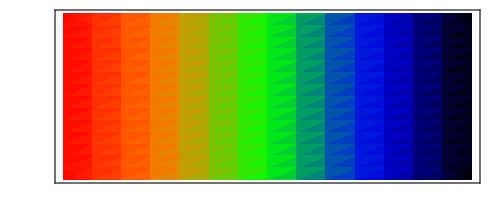

-Graphics-

```mathematica
figure5Jcolorfunction[x_]:=Blend[{Red,Orange,Green,Blue,Black},x]
DensityPlot[
x,{x,0,1},{y,0,0.1},ImageSize->500,PlotRangePadding->None,FrameTicks->None,AspectRatio->Automatic,ColorFunction->figure5Jcolorfunction
]
ColorConvert[%,"Grayscale"]
```

#### Figure 5Jb - momentum semicircle, original

For file size optimization, most of Fig. 5J is rasterized. The original vector versions are kept for completeness, though they produce much bigger files. (This is because they necessarily produce many overlapping points, which the rasterized version treats as single pixels.)

```mathematica
figure5JbOffsetsList=Join[Table[0.015{Sin[θ],Cos[θ]},{θ,0,π,π/6}],Table[0.015{-1,0},{3}]];
Block[{data=halfCircleCircuitTCAdata⟦All⟧,F,ω,κ,indexlist,nl=10},
{F,ω,κ}=figure5Jparameters;
indexlist=Most[Range[1,Length[data],Floor[Length[data]/nl]]];
nl=Length[indexlist];
figure5Jb=Show[Graphics[
(Reverse@Table[
{PointSize[0.009],figure5Jcolorfunction[k/Length[data]],Tooltip[Point[ω/F data⟦k,1,1⟧],k]}
,{k,1,Length[data]}]
)~Join~Table[
{PointSize[0.025],figure5Jcolorfunction[indexlist⟦k⟧/Length[data]],Point[ω/F data⟦indexlist⟦k⟧,1,1⟧]}
,{k,1,nl}]~Join~Table[
Text[Style[ToString[k],7],ω/F data⟦indexlist⟦k⟧,1,1⟧+figure5JbOffsetsList⟦k⟧,{0,0}]
,{k,1,nl}]
]
,AspectRatio->Automatic
,Frame->True
,Axes->True
,AxesStyle->GrayLevel[0.8]
,PlotRange->{ω/F{0,0.2},ω/F{-0.2,0.2}}
,ImageSize->{{700},{200}}
,PlotRangePadding->{Scaled[0.15],Scaled[.075]}
,Method->{"AxesInFront"->False}
,BaseStyle->{FontFamily->"Latin Modern Math"}
,FrameLabel->{MaTeX["\\omega p_x/F",FontSize->9],MaTeX["\\omega p_z/F",FontSize->9]}
,FrameTicks->{{
Join[{#,MaTeX[ToString[PaddedForm[#,{2,1}]],FontSize->9],{0.03,0}}&/@Range[-0.2,0.2,0.1],{#,"",{0.015,0}}&/@Range[-0.2,0.2,0.025]],
Join[{#,"",{0.03,0}}&/@Range[-0.2,0.2,0.1],{#,"",{0.015,0}}&/@Range[-0.2,0.2,0.025]]
},{
Join[{#,MaTeX[ToString[#],FontSize->9],{0.03,0}}&/@{0,0.1,0.2},{#,"",{0.015,0}}&/@Range[-0.1,0.3,0.05],{#,"",{0.008,0}}&/@Range[-0.1,0.3,0.01]],
Join[{#,"",{0.03,0}}&/@{0,0.1,0.2},{#,"",{0.015,0}}&/@Range[-0.1,0.3,0.05],{#,"",{0.008,0}}&/@Range[-0.1,0.3,0.01]]
}}
,ImagePadding->{{Automatic,Scaled[0.001]},{Automatic,0}}
,Epilog->Inset[MaTeX["\\mathrm{(b)}",FontSize->9],Scaled[{-0.22,1}],Scaled[{1,1}]]
]
]
AbsoluteTiming[FileByteCount[Export[$OutputDirectory<>"figure5Jb.pdf",figure5Jb,Background->None]]]
```

{5.48979,350622}

#### Figure 5Jb - momentum semicircle, rasterized

```mathematica
figure5JbOffsetsList=Join[Table[0.015{Sin[θ],Cos[θ]},{θ,0,π,π/6}],Table[0.015{-1,0},{3}]];
Block[{data=halfCircleCircuitTCAdata⟦All⟧,F,ω,κ,indexlist,nl=10,dshape,plotrange},
{F,ω,κ}=figure5Jparameters;
indexlist=Most[Range[1,Length[data],Floor[Length[data]/nl]]];
nl=Length[indexlist];
plotrange=ω/F{{-0.03,0.23},{-0.23,0.23}};
dshape=Rasterize[Show[Graphics[
(Reverse@Table[
{PointSize[0.009],figure5Jcolorfunction[k/Length[data]],Tooltip[Point[ω/F data⟦k,1,1⟧],k]}
,{k,1,Length[data]}]
)~Join~Table[
{PointSize[0.025],figure5Jcolorfunction[indexlist⟦k⟧/Length[data]],Point[ω/F data⟦indexlist⟦k⟧,1,1⟧]}
,{k,1,nl}]]
,PlotRange->plotrange,PlotRangePadding->None,AspectRatio->Automatic],ImageResolution->300];
figure5Jb=Show[{
Graphics[{Inset[dshape,{plotrange⟦1,1⟧,plotrange⟦2,1⟧},{0,0},{plotrange⟦1,2⟧-plotrange⟦1,1⟧,plotrange⟦2,2⟧-plotrange⟦2,1⟧}]}],
Graphics[Table[
Text[Style[ToString[k],7],ω/F data⟦indexlist⟦k⟧,1,1⟧+figure5JbOffsetsList⟦k⟧,{0,0}]
,{k,1,nl}]
]
}
,AspectRatio->Automatic
,Frame->True
,Axes->True
,AxesStyle->GrayLevel[0.8]
,PlotRange->plotrange
,ImageSize->{{700},{200}}
,Method->{"AxesInFront"->False}
,BaseStyle->{FontFamily->"Latin Modern Math"}
,FrameLabel->{MaTeX["\\omega p_x/F",FontSize->9],MaTeX["\\omega p_z/F",FontSize->9]}
,FrameTicks->{{
Join[{#,MaTeX[ToString[PaddedForm[#,{2,1}]],FontSize->9],{0.03,0}}&/@Range[-0.2,0.2,0.1],{#,"",{0.015,0}}&/@Range[-0.2,0.2,0.025]],
Join[{#,"",{0.03,0}}&/@Range[-0.2,0.2,0.1],{#,"",{0.015,0}}&/@Range[-0.2,0.2,0.025]]
},{
Join[{#,MaTeX[ToString[#],FontSize->9],{0.03,0}}&/@{0,0.1,0.2},{#,"",{0.015,0}}&/@Range[-0.1,0.3,0.05],{#,"",{0.008,0}}&/@Range[-0.1,0.3,0.01]],
Join[{#,"",{0.03,0}}&/@{0,0.1,0.2},{#,"",{0.015,0}}&/@Range[-0.1,0.3,0.05],{#,"",{0.008,0}}&/@Range[-0.1,0.3,0.01]]
}}
,ImagePadding->{{Automatic,Scaled[0.001]},{Automatic,0}}
,Epilog->Inset[MaTeX["\\mathrm{(b)}",FontSize->9],Scaled[{-0.22,1}],Scaled[{1,1}]]
]
]
AbsoluteTiming[FileByteCount[Export[$OutputDirectory<>"figure5Jb.pdf",figure5Jb,Background->None]]]
```

{1.26094,68873}

#### Figure 5Jc - time-plane ‘butterfly’, original

For file size optimization, most of Fig. 11 is rasterized. The original vector versions are kept for completeness, though they produce much bigger files. (This is because they necessarily produce many overlapping points, which the rasterized version treats as single pixels.)

```mathematica
figure5JcOffsetsDirections = ({{1, 2, 3, 4, 5, 6, 7, 8, 9, 10}, {-1, -1, -1, 1.5 ⅇ^(-0.1ⅈ), 1.5 ⅇ^(-0.3ⅈ), 1.5 ⅇ^(-0.15ⅈ), 1.5, 1.5, -1, 1.5}, {-1.3 ⅇ^(-0.1ⅈ), -1.3 ⅇ^(-0.3ⅈ), -1, -1, -1, -1, -1, -1, 1.5, -1.3}, {1, 1, 1, 1, 1, 1, 1, 1, 1, 1}})ᵀ⟦All, 2 ;; 4⟧;
Block[{data = halfCircleCircuitTCAdata[[All]], F, ω, κ, 
  indexlist, nl = 10},
 {F, ω, κ} = figure5Jparameters;
 indexlist = Most[Range[1, Length[data], Floor[Length[data]/nl]]];
 nl = Length[indexlist];
 Row[{figure5Jb,
figure5Jc = Show[Graphics[
(Reverse@Table[
Join[{If[MemberQ[indexlist, k], PointSize[0.017],
 PointSize[0.006]], figure5Jcolorfunction[k/Length[data]]},
Tooltip[Point[{Re[ω #], Im[ω #]}], k] & /@ data⟦k, All, 2⟧]
, {k, 1, Length[data]}])~Join~(Table[
Text[
Style[ToString[k],7], {Re[ω #], Im[ω #]}, {0,0}] & /@ (
#1+2. ⅈ figure5JcOffsetsDirections⟦k⟧ (#1 - #2)/Abs[#1 - #2] &[data⟦indexlist⟦k⟧, All, 2⟧,data⟦indexlist⟦k⟧ + 100, All, 2⟧]
)
, {k, 1, nl}])
]
, AspectRatio -> Automatic
, Frame->True
, Axes->True
, AxesStyle->GrayLevel[0.7]
, AxesOrigin->{2 π, 0}
, ImageSize->{{700}, {200}}
, PlotRangePadding->Scaled[0.03]
, Method->{"AxesInFront"->False}
,BaseStyle->{FontFamily->"Latin Modern Math"}
,FrameLabel->{MaTeX["\\mathrm{Re}(\\omega t)",FontSize->9],MaTeX["\\mathrm{Im}(\\omega t)",FontSize->9]}
,FrameTicks->{{
Join[{#,MaTeX[ToString[PaddedForm[#,{2,1}]],FontSize->9],{0.015,0}}&/@Range[-1.5,1.5,0.5],{#,"",{0.008,0}}&/@Range[-2,2,0.1]],
Join[{#,"",{0.015,0}}&/@Range[-1.5,1.5,0.5],{#,"",{0.008,0}}&/@Range[-2,2,0.1]]
},{
Join[
{# π,MaTeX[StringReplace[ToString[Numerator[#]]<>"\\pi/"<>ToString[Denominator[#]],{"/1"->"","1\\pi"->"\\pi","0\\pi"->"0"}],FontSize->9]}&/@Range[7/4,5/2,1/4],
{#,"",{0.008,0}}&/@Range[0,4π,π/16]],
Join[({# π,"",{0.015,0}}&/@Range[0,4,1/4]),({#,"",{0.008,0}}&/@Range[0,4π,π/16])]
}}
,ImagePadding->{{Automatic, Scaled[0.01]}, {Automatic, 0}}
,Epilog->Inset[MaTeX["\\mathrm{(c)}",FontSize->9],Scaled[{-0.17,1}],Scaled[{1,1}]]
]
}]
]
AbsoluteTiming[FileByteCount[Export[$OutputDirectory<>"figure5Jc.pdf",figure5Jc,Background->None]]]
```

{10.3391,995134}

#### Figure 5Jc - time-plane ‘butterfly’, rasterized

```mathematica
{Re[#],Im[#]}&/@halfCircleCircuitTCAdata⟦All,1,2⟧
```

```mathematica
figure5JcOffsetsDirections = ({{1, 2, 3, 4, 5, 6, 7, 8, 9, 10}, {-1, -1, -1, 1.5 ⅇ^(-0.1ⅈ), 1.5 ⅇ^(-0.3ⅈ), 1.5 ⅇ^(-0.15ⅈ), 1.5, 1.5, -1, 1.5}, {-1.3 ⅇ^(-0.1ⅈ), -1.3 ⅇ^(-0.3ⅈ), -1, -1, -1, -1, -1, -1, 1.5, -1.3}, {1, 1, 1, 1, 1, 1, 1, 1, 1, 1}})ᵀ⟦All, 2 ;; 4⟧;
Block[{data=halfCircleCircuitTCAdata⟦All⟧,F,ω,κ,indexlist,nl=10,butterfly,plotrange},
{F,ω,κ}=figure5Jparameters;
indexlist=Most[Range[1,Length[data],Floor[Length[data]/nl]]];
nl=Length[indexlist];
plotrange={{5.12,7.95},{-1.65,1.65}};
butterfly=Rasterize[Show[
Graphics[
(Reverse@Table[
Join[{If[MemberQ[indexlist,k],PointSize[0.017],PointSize[0.006]],figure5Jcolorfunction[k/Length[data]]},Point[{Re[ω #],Im[ω #]}]&/@data⟦k,All,2⟧]
,{k,1,Length[data]}])]
,PlotRange->plotrange,PlotRangePadding->None,AspectRatio->Automatic],ImageResolution->300];
AbsoluteTiming[
figure5Jc=Show[{
Graphics[{Inset[butterfly,{plotrange⟦1,1⟧,plotrange⟦2,1⟧},{0,0},{plotrange⟦1,2⟧-plotrange⟦1,1⟧,plotrange⟦2,2⟧-plotrange⟦2,1⟧}]}],
Graphics[(Table[
Text[Style[ToString[k],7],{Re[ω #],Im[ω #]},{0,0}]&/@(#1+2.ⅈ figure5JcOffsetsDirections⟦k⟧(#1-#2)/Abs[#1-#2]&[data⟦indexlist⟦k⟧,All,2⟧,data⟦indexlist⟦k⟧+100,All,2⟧])
,{k,1,nl}])
]}
,AspectRatio->Automatic
,Frame->True
,Axes->True
,AxesStyle->GrayLevel[0.7]
,AxesOrigin->{2π,0}
,ImageSize->{{700},{200}}
,PlotRange->plotrange
,PlotRangePadding->Scaled[0.02]
,Method->{"AxesInFront"->False}
,BaseStyle->{FontFamily->"Latin Modern Math"}
,FrameLabel->{MaTeX["\\mathrm{Re}(\\omega t)",FontSize->9],MaTeX["\\mathrm{Im}(\\omega t)",FontSize->9]}
,FrameTicks->{{
Join[{#,MaTeX[ToString[PaddedForm[#,{2,1}]],FontSize->9],{0.015,0}}&/@Range[-1.5,1.5,0.5],{#,"",{0.008,0}}&/@Range[-2,2,0.1]],
Join[{#,"",{0.015,0}}&/@Range[-1.5,1.5,0.5],{#,"",{0.008,0}}&/@Range[-2,2,0.1]]
},{
Join[
{# π,MaTeX[StringReplace[ToString[Numerator[#]]<>"\\pi/"<>ToString[Denominator[#]],{"/1"->"","1\\pi"->"\\pi","0\\pi"->"0"}],FontSize->9]}&/@Range[7/4,5/2,1/4],
{#,"",{0.008,0}}&/@Range[0,4π,π/16]],
Join[({# π,"",{0.015,0}}&/@Range[0,4,1/4]),({#,"",{0.008,0}}&/@Range[0,4π,π/16])]
}}
,ImagePadding->{{Automatic, Scaled[0.01]}, {Automatic, 0}}
,Epilog->Inset[MaTeX["\\mathrm{(c)}",FontSize->9],Scaled[{-0.17,1}],Scaled[{1,1}]]
];
]
]
Row[{figure5Jb,figure5Jc}]
AbsoluteTiming[FileByteCount[Export[$OutputDirectory<>"figure5Jc.pdf",figure5Jc,Background->None]]]
```

{2.91421,Null}

{2.08159,97913}

#### Exporting fig. 5Jb and5Jc

```mathematica
AbsoluteTiming[FileByteCount[Export[$OutputDirectory<>"figure5Jb.pdf",Show[figure5Jb,ImageSize->{{700},{200}}],Background->None]]]
AbsoluteTiming[FileByteCount[Export[$OutputDirectory<>"figure5Jc.pdf",Show[figure5Jc,ImageSize->{{700},{200}}],Background->None]]]
```

{4.44194,342628}

{10.2511,987504}

#### Figure 5Jc with no axes

```mathematica
figure5JcOffsetsDirections = ({{1, 2, 3, 4, 5, 6, 7, 8, 9, 10}, {-1, -1, -1, 1.5 ⅇ^(-0.1ⅈ), 1.5 ⅇ^(-0.3ⅈ), 1.5 ⅇ^(-0.15ⅈ), 1.5, 1.5, -1, 1.5}, {-1.3 ⅇ^(-0.1ⅈ), -1.3 ⅇ^(-0.3ⅈ), -1, -1, -1, -1, -1, -1, 1.5, -1.3}, {1, 1, 1, 1, 1, 1, 1, 1, 1, 1}})ᵀ⟦All, 2 ;; 4⟧;
Block[{data=halfCircleCircuitTCAdata⟦All⟧,F,ω,κ,indexlist,nl=10,butterfly,plotrange},
{F,ω,κ}=figure5Jparameters;
indexlist=Most[Range[1,Length[data],Floor[Length[data]/nl]]];
nl=Length[indexlist];
plotrange={{5.12,7.95},{-1.65,1.65}};
butterfly=Rasterize[Show[
Graphics[
(Reverse@Table[
Join[{If[MemberQ[indexlist,k],PointSize[0.017],PointSize[0.006]],figure5Jcolorfunction[k/Length[data]]},Point[{Re[ω #],Im[ω #]}]&/@data⟦k,All,2⟧]
,{k,1,Length[data]}])]
,PlotRange->plotrange,PlotRangePadding->None,AspectRatio->Automatic],ImageResolution->300];
figure5JcNoAxes=Show[{
Graphics[{Inset[butterfly,{plotrange⟦1,1⟧,plotrange⟦2,1⟧},{0,0},{plotrange⟦1,2⟧-plotrange⟦1,1⟧,plotrange⟦2,2⟧-plotrange⟦2,1⟧}]}],
Graphics[(Table[
Text[Style[ToString[k],12],{Re[ω #],Im[ω #]},{0,0}]&/@(#1+2.ⅈ figure5JcOffsetsDirections⟦k⟧(#1-#2)/Abs[#1-#2]&[data⟦indexlist⟦k⟧,All,2⟧,data⟦indexlist⟦k⟧+100,All,2⟧])
,{k,1,nl}])
]}
,AspectRatio->Automatic
,Frame->False
,Axes->False
,ImageSize->{{700},{500}}
,PlotRange->plotrange
,PlotRangePadding->Scaled[.02]
,Method->{"AxesInFront"->False}
]
]
FileByteCount[Export[$OutputDirectory<>"figure5JcNoAxes.png",figure5JcNoAxes]]
```

21841